```mathematica
Series[(1+(1-θ)ν L)/(1-θ ν L),{L,0,5}]
```

1+ν L+θ ν^2 L^2+θ^2 ν^3 L^3+θ^3 ν^4 L^4+θ^4 ν^5 L^5+O[L]^6

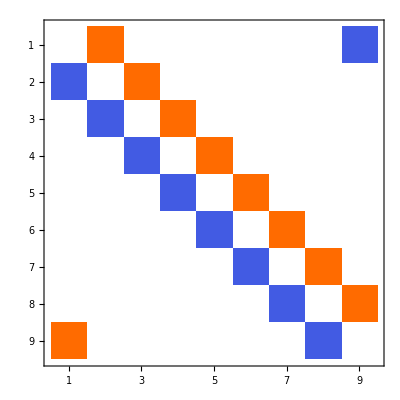
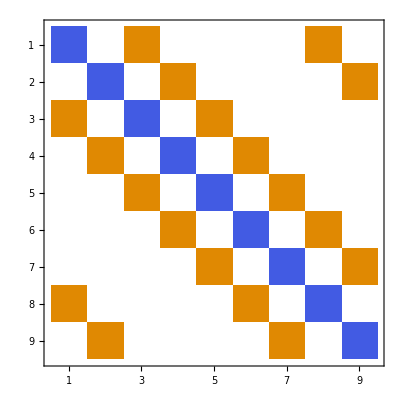
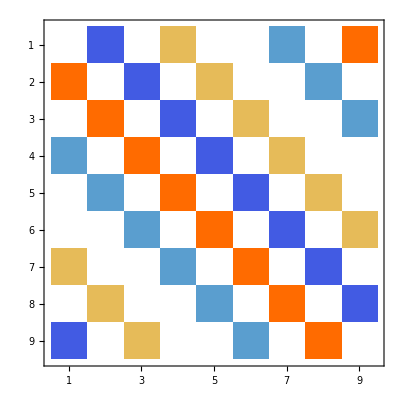
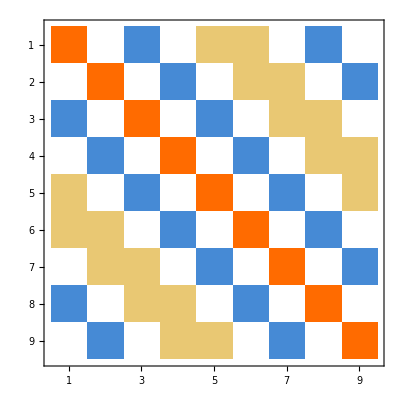
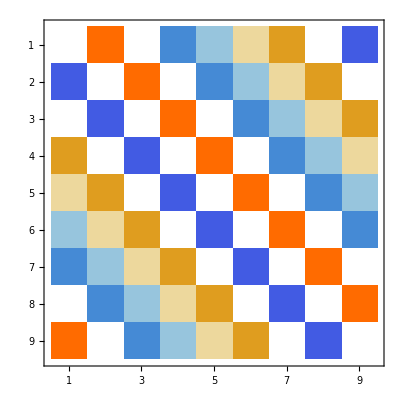
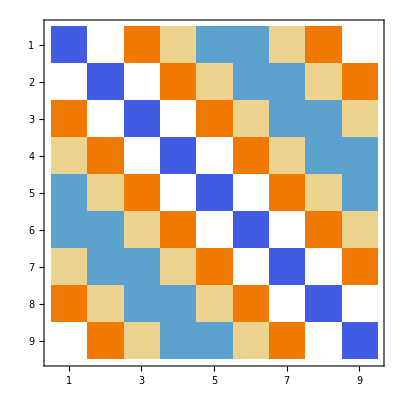
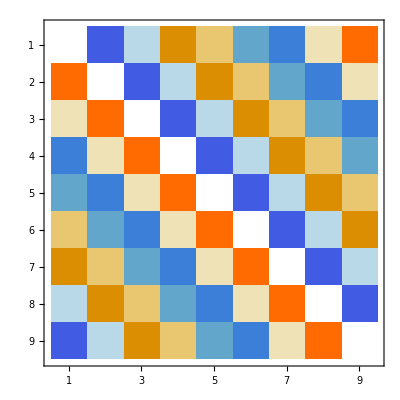
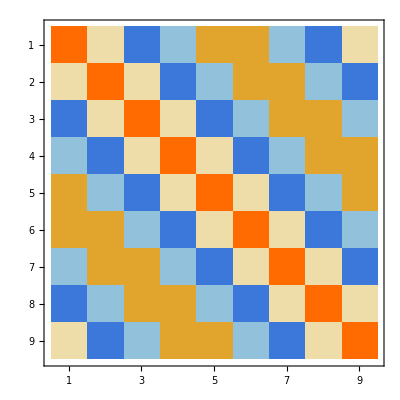
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{m=9},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixPlot@MatrixPower[A,power],{power,1,50}]]
```

```mathematica
With[{m=9},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@MatrixPower[A,power],{power,1,50}]]
```

{(0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
1/2 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0),(-1/2 | 0 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 0
0 | -1/2 | 0 | 1/4 | 0 | 0 | 0 | 0 | 1/4
1/4 | 0 | -1/2 | 0 | 1/4 | 0 | 0 | 0 | 0
0 | 1/4 | 0 | -1/2 | 0 | 1/4 | 0 | 0 | 0
0 | 0 | 1/4 | 0 | -1/2 | 0 | 1/4 | 0 | 0
0 | 0 | 0 | 1/4 | 0 | -1/2 | 0 | 1/4 | 0
0 | 0 | 0 | 0 | 1/4 | 0 | -1/2 | 0 | 1/4
1/4 | 0 | 0 | 0 | 0 | 1/4 | 0 | -1/2 | 0
0 | 1/4 | 0 | 0 | 0 | 0 | 1/4 | 0 | -1/2),(0 | -3/8 | 0 | 1/8 | 0 | 0 | -1/8 | 0 | 3/8
3/8 | 0 | -3/8 | 0 | 1/8 | 0 | 0 | -1/8 | 0
0 | 3/8 | 0 | -3/8 | 0 | 1/8 | 0 | 0 | -1/8
-1/8 | 0 | 3/8 | 0 | -3/8 | 0 | 1/8 | 0 | 0
0 | -1/8 | 0 | 3/8 | 0 | -3/8 | 0 | 1/8 | 0
0 | 0 | -1/8 | 0 | 3/8 | 0 | -3/8 | 0 | 1/8
1/8 | 0 | 0 | -1/8 | 0 | 3/8 | 0 | -3/8 | 0
0 | 1/8 | 0 | 0 | -1/8 | 0 | 3/8 | 0 | -3/8
-3/8 | 0 | 1/8 | 0 | 0 | -1/8 | 0 | 3/8 | 0),(3/8 | 0 | -1/4 | 0 | 1/16 | 1/16 | 0 | -1/4 | 0
0 | 3/8 | 0 | -1/4 | 0 | 1/16 | 1/16 | 0 | -1/4
-1/4 | 0 | 3/8 | 0 | -1/4 | 0 | 1/16 | 1/16 | 0
0 | -1/4 | 0 | 3/8 | 0 | -1/4 | 0 | 1/16 | 1/16
1/16 | 0 | -1/4 | 0 | 3/8 | 0 | -1/4 | 0 | 1/16
1/16 | 1/16 | 0 | -1/4 | 0 | 3/8 | 0 | -1/4 | 0
0 | 1/16 | 1/16 | 0 | -1/4 | 0 | 3/8 | 0 | -1/4
-1/4 | 0 | 1/16 | 1/16 | 0 | -1/4 | 0 | 3/8 | 0
0 | -1/4 | 0 | 1/16 | 1/16 | 0 | -1/4 | 0 | 3/8),(0 | 5/16 | 0 | -5/32 | -1/32 | 1/32 | 5/32 | 0 | -5/16
-5/16 | 0 | 5/16 | 0 | -5/32 | -1/32 | 1/32 | 5/32 | 0
0 | -5/16 | 0 | 5/16 | 0 | -5/32 | -1/32 | 1/32 | 5/32
5/32 | 0 | -5/16 | 0 | 5/16 | 0 | -5/32 | -1/32 | 1/32
1/32 | 5/32 | 0 | -5/16 | 0 | 5/16 | 0 | -5/32 | -1/32
-1/32 | 1/32 | 5/32 | 0 | -5/16 | 0 | 5/16 | 0 | -5/32
-5/32 | -1/32 | 1/32 | 5/32 | 0 | -5/16 | 0 | 5/16 | 0
0 | -5/32 | -1/32 | 1/32 | 5/32 | 0 | -5/16 | 0 | 5/16
5/16 | 0 | -5/32 | -1/32 | 1/32 | 5/32 | 0 | -5/16 | 0),(-5/16 | 0 | 15/64 | 1/64 | -3/32 | -3/32 | 1/64 | 15/64 | 0
0 | -5/16 | 0 | 15/64 | 1/64 | -3/32 | -3/32 | 1/64 | 15/64
15/64 | 0 | -5/16 | 0 | 15/64 | 1/64 | -3/32 | -3/32 | 1/64
1/64 | 15/64 | 0 | -5/16 | 0 | 15/64 | 1/64 | -3/32 | -3/32
-3/32 | 1/64 | 15/64 | 0 | -5/16 | 0 | 15/64 | 1/64 | -3/32
-3/32 | -3/32 | 1/64 | 15/64 | 0 | -5/16 | 0 | 15/64 | 1/64
1/64 | -3/32 | -3/32 | 1/64 | 15/64 | 0 | -5/16 | 0 | 15/64
15/64 | 1/64 | -3/32 | -3/32 | 1/64 | 15/64 | 0 | -5/16 | 0
0 | 15/64 | 1/64 | -3/32 | -3/32 | 1/64 | 15/64 | 0 | -5/16),(0 | -35/128 | -1/128 | 21/128 | 7/128 | -7/128 | -21/128 | 1/128 | 35/128
35/128 | 0 | -35/128 | -1/128 | 21/128 | 7/128 | -7/128 | -21/128 | 1/128
1/128 | 35/128 | 0 | -35/128 | -1/128 | 21/128 | 7/128 | -7/128 | -21/128
-21/128 | 1/128 | 35/128 | 0 | -35/128 | -1/128 | 21/128 | 7/128 | -7/128
-7/128 | -21/128 | 1/128 | 35/128 | 0 | -35/128 | -1/128 | 21/128 | 7/128
7/128 | -7/128 | -21/128 | 1/128 | 35/128 | 0 | -35/128 | -1/128 | 21/128
21/128 | 7/128 | -7/128 | -21/128 | 1/128 | 35/128 | 0 | -35/128 | -1/128
-1/128 | 21/128 | 7/128 | -7/128 | -21/128 | 1/128 | 35/128 | 0 | -35/128
-35/128 | -1/128 | 21/128 | 7/128 | -7/128 | -21/128 | 1/128 | 35/128 | 0),(35/128 | 1/256 | -7/32 | -1/32 | 7/64 | 7/64 | -1/32 | -7/32 | 1/256
1/256 | 35/128 | 1/256 | -7/32 | -1/32 | 7/64 | 7/64 | -1/32 | -7/32
-7/32 | 1/256 | 35/128 | 1/256 | -7/32 | -1/32 | 7/64 | 7/64 | -1/32
-1/32 | -7/32 | 1/256 | 35/128 | 1/256 | -7/32 | -1/32 | 7/64 | 7/64
7/64 | -1/32 | -7/32 | 1/256 | 35/128 | 1/256 | -7/32 | -1/32 | 7/64
7/64 | 7/64 | -1/32 | -7/32 | 1/256 | 35/128 | 1/256 | -7/32 | -1/32
-1/32 | 7/64 | 7/64 | -1/32 | -7/32 | 1/256 | 35/128 | 1/256 | -7/32
-7/32 | -1/32 | 7/64 | 7/64 | -1/32 | -7/32 | 1/256 | 35/128 | 1/256
1/256 | -7/32 | -1/32 | 7/64 | 7/64 | -1/32 | -7/32 | 1/256 | 35/128),(0 | 63/256 | 9/512 | -21/128 | -9/128 | 9/128 | 21/128 | -9/512 | -63/256
-63/256 | 0 | 63/256 | 9/512 | -21/128 | -9/128 | 9/128 | 21/128 | -9/512
-9/512 | -63/256 | 0 | 63/256 | 9/512 | -21/128 | -9/128 | 9/128 | 21/128
21/128 | -9/512 | -63/256 | 0 | 63/256 | 9/512 | -21/128 | -9/128 | 9/128
9/128 | 21/128 | -9/512 | -63/256 | 0 | 63/256 | 9/512 | -21/128 | -9/128
-9/128 | 9/128 | 21/128 | -9/512 | -63/256 | 0 | 63/256 | 9/512 | -21/128
-21/128 | -9/128 | 9/128 | 21/128 | -9/512 | -63/256 | 0 | 63/256 | 9/512
9/512 | -21/128 | -9/128 | 9/128 | 21/128 | -9/512 | -63/256 | 0 | 63/256
63/256 | 9/512 | -21/128 | -9/128 | 9/128 | 21/128 | -9/512 | -63/256 | 0),(-63/256 | -9/1024 | 105/512 | 45/1024 | -15/128 | -15/128 | 45/1024 | 105/512 | -9/1024
-9/1024 | -63/256 | -9/1024 | 105/512 | 45/1024 | -15/128 | -15/128 | 45/1024 | 105/512
105/512 | -9/1024 | -63/256 | -9/1024 | 105/512 | 45/1024 | -15/128 | -15/128 | 45/1024
45/1024 | 105/512 | -9/1024 | -63/256 | -9/1024 | 105/512 | 45/1024 | -15/128 | -15/128
-15/128 | 45/1024 | 105/512 | -9/1024 | -63/256 | -9/1024 | 105/512 | 45/1024 | -15/128
-15/128 | -15/128 | 45/1024 | 105/512 | -9/1024 | -63/256 | -9/1024 | 105/512 | 45/1024
45/1024 | -15/128 | -15/128 | 45/1024 | 105/512 | -9/1024 | -63/256 | -9/1024 | 105/512
105/512 | 45/1024 | -15/128 | -15/128 | 45/1024 | 105/512 | -9/1024 | -63/256 | -9/1024
-9/1024 | 105/512 | 45/1024 | -15/128 | -15/128 | 45/1024 | 105/512 | -9/1024 | -63/256),(0 | -231/1024 | -27/1024 | 165/1024 | 165/2048 | -165/2048 | -165/1024 | 27/1024 | 231/1024
231/1024 | 0 | -231/1024 | -27/1024 | 165/1024 | 165/2048 | -165/2048 | -165/1024 | 27/1024
27/1024 | 231/1024 | 0 | -231/1024 | -27/1024 | 165/1024 | 165/2048 | -165/2048 | -165/1024
-165/1024 | 27/1024 | 231/1024 | 0 | -231/1024 | -27/1024 | 165/1024 | 165/2048 | -165/2048
-165/2048 | -165/1024 | 27/1024 | 231/1024 | 0 | -231/1024 | -27/1024 | 165/1024 | 165/2048
165/2048 | -165/2048 | -165/1024 | 27/1024 | 231/1024 | 0 | -231/1024 | -27/1024 | 165/1024
165/1024 | 165/2048 | -165/2048 | -165/1024 | 27/1024 | 231/1024 | 0 | -231/1024 | -27/1024
-27/1024 | 165/1024 | 165/2048 | -165/2048 | -165/1024 | 27/1024 | 231/1024 | 0 | -231/1024
-231/1024 | -27/1024 | 165/1024 | 165/2048 | -165/2048 | -165/1024 | 27/1024 | 231/1024 | 0),(231/1024 | 27/2048 | -99/512 | -219/4096 | 495/4096 | 495/4096 | -219/4096 | -99/512 | 27/2048
27/2048 | 231/1024 | 27/2048 | -99/512 | -219/4096 | 495/4096 | 495/4096 | -219/4096 | -99/512
-99/512 | 27/2048 | 231/1024 | 27/2048 | -99/512 | -219/4096 | 495/4096 | 495/4096 | -219/4096
-219/4096 | -99/512 | 27/2048 | 231/1024 | 27/2048 | -99/512 | -219/4096 | 495/4096 | 495/4096
495/4096 | -219/4096 | -99/512 | 27/2048 | 231/1024 | 27/2048 | -99/512 | -219/4096 | 495/4096
495/4096 | 495/4096 | -219/4096 | -99/512 | 27/2048 | 231/1024 | 27/2048 | -99/512 | -219/4096
-219/4096 | 495/4096 | 495/4096 | -219/4096 | -99/512 | 27/2048 | 231/1024 | 27/2048 | -99/512
-99/512 | -219/4096 | 495/4096 | 495/4096 | -219/4096 | -99/512 | 27/2048 | 231/1024 | 27/2048
27/2048 | -99/512 | -219/4096 | 495/4096 | 495/4096 | -219/4096 | -99/512 | 27/2048 | 231/1024),(0 | 429/2048 | 273/8192 | -1287/8192 | -357/4096 | 357/4096 | 1287/8192 | -273/8192 | -429/2048
-429/2048 | 0 | 429/2048 | 273/8192 | -1287/8192 | -357/4096 | 357/4096 | 1287/8192 | -273/8192
-273/8192 | -429/2048 | 0 | 429/2048 | 273/8192 | -1287/8192 | -357/4096 | 357/4096 | 1287/8192
1287/8192 | -273/8192 | -429/2048 | 0 | 429/2048 | 273/8192 | -1287/8192 | -357/4096 | 357/4096
357/4096 | 1287/8192 | -273/8192 | -429/2048 | 0 | 429/2048 | 273/8192 | -1287/8192 | -357/4096
-357/4096 | 357/4096 | 1287/8192 | -273/8192 | -429/2048 | 0 | 429/2048 | 273/8192 | -1287/8192
-1287/8192 | -357/4096 | 357/4096 | 1287/8192 | -273/8192 | -429/2048 | 0 | 429/2048 | 273/8192
273/8192 | -1287/8192 | -357/4096 | 357/4096 | 1287/8192 | -273/8192 | -429/2048 | 0 | 429/2048
429/2048 | 273/8192 | -1287/8192 | -357/4096 | 357/4096 | 1287/8192 | -273/8192 | -429/2048 | 0),(-429/2048 | -273/16384 | 3003/16384 | 987/16384 | -2001/16384 | -2001/16384 | 987/16384 | 3003/16384 | -273/16384
-273/16384 | -429/2048 | -273/16384 | 3003/16384 | 987/16384 | -2001/16384 | -2001/16384 | 987/16384 | 3003/16384
3003/16384 | -273/16384 | -429/2048 | -273/16384 | 3003/16384 | 987/16384 | -2001/16384 | -2001/16384 | 987/16384
987/16384 | 3003/16384 | -273/16384 | -429/2048 | -273/16384 | 3003/16384 | 987/16384 | -2001/16384 | -2001/16384
-2001/16384 | 987/16384 | 3003/16384 | -273/16384 | -429/2048 | -273/16384 | 3003/16384 | 987/16384 | -2001/16384
-2001/16384 | -2001/16384 | 987/16384 | 3003/16384 | -273/16384 | -429/2048 | -273/16384 | 3003/16384 | 987/16384
987/16384 | -2001/16384 | -2001/16384 | 987/16384 | 3003/16384 | -273/16384 | -429/2048 | -273/16384 | 3003/16384
3003/16384 | 987/16384 | -2001/16384 | -2001/16384 | 987/16384 | 3003/16384 | -273/16384 | -429/2048 | -273/16384
-273/16384 | 3003/16384 | 987/16384 | -2001/16384 | -2001/16384 | 987/16384 | 3003/16384 | -273/16384 | -429/2048),(0 | -6435/32768 | -315/8192 | 1251/8192 | 747/8192 | -747/8192 | -1251/8192 | 315/8192 | 6435/32768
6435/32768 | 0 | -6435/32768 | -315/8192 | 1251/8192 | 747/8192 | -747/8192 | -1251/8192 | 315/8192
315/8192 | 6435/32768 | 0 | -6435/32768 | -315/8192 | 1251/8192 | 747/8192 | -747/8192 | -1251/8192
-1251/8192 | 315/8192 | 6435/32768 | 0 | -6435/32768 | -315/8192 | 1251/8192 | 747/8192 | -747/8192
-747/8192 | -1251/8192 | 315/8192 | 6435/32768 | 0 | -6435/32768 | -315/8192 | 1251/8192 | 747/8192
747/8192 | -747/8192 | -1251/8192 | 315/8192 | 6435/32768 | 0 | -6435/32768 | -315/8192 | 1251/8192
1251/8192 | 747/8192 | -747/8192 | -1251/8192 | 315/8192 | 6435/32768 | 0 | -6435/32768 | -315/8192
-315/8192 | 1251/8192 | 747/8192 | -747/8192 | -1251/8192 | 315/8192 | 6435/32768 | 0 | -6435/32768
-6435/32768 | -315/8192 | 1251/8192 | 747/8192 | -747/8192 | -1251/8192 | 315/8192 | 6435/32768 | 0),(6435/32768 | 315/16384 | -11439/65536 | -531/8192 | 999/8192 | 999/8192 | -531/8192 | -11439/65536 | 315/16384
315/16384 | 6435/32768 | 315/16384 | -11439/65536 | -531/8192 | 999/8192 | 999/8192 | -531/8192 | -11439/65536
-11439/65536 | 315/16384 | 6435/32768 | 315/16384 | -11439/65536 | -531/8192 | 999/8192 | 999/8192 | -531/8192
-531/8192 | -11439/65536 | 315/16384 | 6435/32768 | 315/16384 | -11439/65536 | -531/8192 | 999/8192 | 999/8192
999/8192 | -531/8192 | -11439/65536 | 315/16384 | 6435/32768 | 315/16384 | -11439/65536 | -531/8192 | 999/8192
999/8192 | 999/8192 | -531/8192 | -11439/65536 | 315/16384 | 6435/32768 | 315/16384 | -11439/65536 | -531/8192
-531/8192 | 999/8192 | 999/8192 | -531/8192 | -11439/65536 | 315/16384 | 6435/32768 | 315/16384 | -11439/65536
-11439/65536 | -531/8192 | 999/8192 | 999/8192 | -531/8192 | -11439/65536 | 315/16384 | 6435/32768 | 315/16384
315/16384 | -11439/65536 | -531/8192 | 999/8192 | 999/8192 | -531/8192 | -11439/65536 | 315/16384 | 6435/32768),(0 | 24309/131072 | 1377/32768 | -19431/131072 | -765/8192 | 765/8192 | 19431/131072 | -1377/32768 | -24309/131072
-24309/131072 | 0 | 24309/131072 | 1377/32768 | -19431/131072 | -765/8192 | 765/8192 | 19431/131072 | -1377/32768
-1377/32768 | -24309/131072 | 0 | 24309/131072 | 1377/32768 | -19431/131072 | -765/8192 | 765/8192 | 19431/131072
19431/131072 | -1377/32768 | -24309/131072 | 0 | 24309/131072 | 1377/32768 | -19431/131072 | -765/8192 | 765/8192
765/8192 | 19431/131072 | -1377/32768 | -24309/131072 | 0 | 24309/131072 | 1377/32768 | -19431/131072 | -765/8192
-765/8192 | 765/8192 | 19431/131072 | -1377/32768 | -24309/131072 | 0 | 24309/131072 | 1377/32768 | -19431/131072
-19431/131072 | -765/8192 | 765/8192 | 19431/131072 | -1377/32768 | -24309/131072 | 0 | 24309/131072 | 1377/32768
1377/32768 | -19431/131072 | -765/8192 | 765/8192 | 19431/131072 | -1377/32768 | -24309/131072 | 0 | 24309/131072
24309/131072 | 1377/32768 | -19431/131072 | -765/8192 | 765/8192 | 19431/131072 | -1377/32768 | -24309/131072 | 0),(-24309/131072 | -1377/65536 | 10935/65536 | 4437/65536 | -31671/262144 | -31671/262144 | 4437/65536 | 10935/65536 | -1377/65536
-1377/65536 | -24309/131072 | -1377/65536 | 10935/65536 | 4437/65536 | -31671/262144 | -31671/262144 | 4437/65536 | 10935/65536
10935/65536 | -1377/65536 | -24309/131072 | -1377/65536 | 10935/65536 | 4437/65536 | -31671/262144 | -31671/262144 | 4437/65536
4437/65536 | 10935/65536 | -1377/65536 | -24309/131072 | -1377/65536 | 10935/65536 | 4437/65536 | -31671/262144 | -31671/262144
-31671/262144 | 4437/65536 | 10935/65536 | -1377/65536 | -24309/131072 | -1377/65536 | 10935/65536 | 4437/65536 | -31671/262144
-31671/262144 | -31671/262144 | 4437/65536 | 10935/65536 | -1377/65536 | -24309/131072 | -1377/65536 | 10935/65536 | 4437/65536
4437/65536 | -31671/262144 | -31671/262144 | 4437/65536 | 10935/65536 | -1377/65536 | -24309/131072 | -1377/65536 | 10935/65536
10935/65536 | 4437/65536 | -31671/262144 | -31671/262144 | 4437/65536 | 10935/65536 | -1377/65536 | -24309/131072 | -1377/65536
-1377/65536 | 10935/65536 | 4437/65536 | -31671/262144 | -31671/262144 | 4437/65536 | 10935/65536 | -1377/65536 | -24309/131072),(0 | -46179/262144 | -2907/65536 | 75411/524288 | 49419/524288 | -49419/524288 | -75411/524288 | 2907/65536 | 46179/262144
46179/262144 | 0 | -46179/262144 | -2907/65536 | 75411/524288 | 49419/524288 | -49419/524288 | -75411/524288 | 2907/65536
2907/65536 | 46179/262144 | 0 | -46179/262144 | -2907/65536 | 75411/524288 | 49419/524288 | -49419/524288 | -75411/524288
-75411/524288 | 2907/65536 | 46179/262144 | 0 | -46179/262144 | -2907/65536 | 75411/524288 | 49419/524288 | -49419/524288
-49419/524288 | -75411/524288 | 2907/65536 | 46179/262144 | 0 | -46179/262144 | -2907/65536 | 75411/524288 | 49419/524288
49419/524288 | -49419/524288 | -75411/524288 | 2907/65536 | 46179/262144 | 0 | -46179/262144 | -2907/65536 | 75411/524288
75411/524288 | 49419/524288 | -49419/524288 | -75411/524288 | 2907/65536 | 46179/262144 | 0 | -46179/262144 | -2907/65536
-2907/65536 | 75411/524288 | 49419/524288 | -49419/524288 | -75411/524288 | 2907/65536 | 46179/262144 | 0 | -46179/262144
-46179/262144 | -2907/65536 | 75411/524288 | 49419/524288 | -49419/524288 | -75411/524288 | 2907/65536 | 46179/262144 | 0),(46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072
2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576
-167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576
-72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288
62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288
62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576 | -72675/1048576
-72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072 | -167769/1048576
-167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144 | 2907/131072
2907/131072 | -167769/1048576 | -72675/1048576 | 62415/524288 | 62415/524288 | -72675/1048576 | -167769/1048576 | 2907/131072 | 46179/262144),(0 | 352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152
-352485/2097152 | 0 | 352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152
-95931/2097152 | -352485/2097152 | 0 | 352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152
292599/2097152 | -95931/2097152 | -352485/2097152 | 0 | 352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152
197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152 | 0 | 352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152
-197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152 | 0 | 352485/2097152 | 95931/2097152 | -292599/2097152
-292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152 | 0 | 352485/2097152 | 95931/2097152
95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152 | 0 | 352485/2097152
352485/2097152 | 95931/2097152 | -292599/2097152 | -197505/2097152 | 197505/2097152 | 292599/2097152 | -95931/2097152 | -352485/2097152 | 0),(-352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304
-95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576
161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576
73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288
-61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288
-61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576 | 73359/1048576
73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304 | 161271/1048576
161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152 | -95931/4194304
-95931/4194304 | 161271/1048576 | 73359/1048576 | -61263/524288 | -61263/524288 | 73359/1048576 | 161271/1048576 | -95931/4194304 | -352485/2097152),(0 | -675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304
675027/4194304 | 0 | -675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608
389367/8388608 | 675027/4194304 | 0 | -675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152
-283797/2097152 | 389367/8388608 | 675027/4194304 | 0 | -675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152
-195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304 | 0 | -675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152
195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304 | 0 | -675027/4194304 | -389367/8388608 | 283797/2097152
283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304 | 0 | -675027/4194304 | -389367/8388608
-389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304 | 0 | -675027/4194304
-675027/4194304 | -389367/8388608 | 283797/2097152 | 195885/2097152 | -195885/2097152 | -283797/2097152 | 389367/8388608 | 675027/4194304 | 0),(675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216
389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608
-1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216
-1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152
239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152
239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608 | -1172907/16777216
-1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216 | -1242621/8388608
-1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304 | 389367/16777216
389367/16777216 | -1242621/8388608 | -1172907/16777216 | 239841/2097152 | 239841/2097152 | -1172907/16777216 | -1242621/8388608 | 389367/16777216 | 675027/4194304),(0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216
-2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216
-781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216
2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432
3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432
-3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216 | -2201985/16777216
-2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216 | 781137/16777216
781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0 | 2592675/16777216
2592675/16777216 | 781137/16777216 | -2201985/16777216 | -3091635/33554432 | 3091635/33554432 | 2201985/16777216 | -781137/16777216 | -2592675/16777216 | 0),(-2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432
-781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608
1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864
4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864
-7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864
-7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608 | 4653909/67108864
4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432 | 1198665/8388608
1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216 | -781137/33554432
-781137/33554432 | 1198665/8388608 | 4653909/67108864 | -7495605/67108864 | -7495605/67108864 | 4653909/67108864 | 1198665/8388608 | -781137/33554432 | -2592675/16777216),(0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432
4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728
6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728
-17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864
-6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864
6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728 | 17084925/134217728
17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432 | -6216183/134217728
-6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0 | -4990005/33554432
-4990005/33554432 | -6216183/134217728 | 17084925/134217728 | 6074757/67108864 | -6074757/67108864 | -17084925/134217728 | 6216183/134217728 | 4990005/33554432 | 0),(4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456
6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456
-37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456
-18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456
29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456
29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456 | -18365697/268435456
-18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456 | -37044945/268435456
-37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432 | 6216183/268435456
6216183/268435456 | -37044945/268435456 | -18365697/268435456 | 29234439/268435456 | 29234439/268435456 | -18365697/268435456 | -37044945/268435456 | 6216183/268435456 | 4990005/33554432),(0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912
-76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864
-3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864
8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864
5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864
-5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864 | -8284923/67108864
-8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912 | 3072735/67108864
3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0 | 76964985/536870912
76964985/536870912 | 3072735/67108864 | -8284923/67108864 | -5950017/67108864 | 5950017/67108864 | 8284923/67108864 | -3072735/67108864 | -76964985/536870912 | 0),(-76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728
-3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824
143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304
281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432
-3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432
-3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824 | 281961/4194304
281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728 | 143244369/1073741824
143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912 | -3072735/134217728
-3072735/134217728 | 143244369/1073741824 | 281961/4194304 | -3558735/33554432 | -3558735/33554432 | 281961/4194304 | 143244369/1073741824 | -3072735/134217728 | -76964985/536870912),(0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648
297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456
12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648
-257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864
-5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864
5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456 | 257123889/2147483648
257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648 | -12095487/268435456
-12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0 | -297174339/2147483648
-297174339/2147483648 | -12095487/268435456 | 257123889/2147483648 | 5814423/67108864 | -5814423/67108864 | -257123889/2147483648 | 12095487/268435456 | 297174339/2147483648 | 0),(297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912
12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824
-138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912
-35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296
443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296
443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824 | -35353179/536870912
-35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912 | -138574557/1073741824
-138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648 | 12095487/536870912
12095487/536870912 | -138574557/1073741824 | -35353179/536870912 | 443185425/4294967296 | 443185425/4294967296 | -35353179/536870912 | -138574557/1073741824 | 12095487/536870912 | 297174339/2147483648),(0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296
-574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912
-23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592
997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592
726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592
-726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912 | -997483653/8589934592
-997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296 | 23724333/536870912
23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0 | 574323453/4294967296
574323453/4294967296 | 23724333/536870912 | -997483653/8589934592 | -726010857/8589934592 | 726010857/8589934592 | 997483653/8589934592 | -23724333/536870912 | -574323453/4294967296 | 0),(-574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824
-23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184
2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184
1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592
-861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592
-861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184
1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824 | 2146130559/17179869184
2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296 | -23724333/1073741824
-23724333/1073741824 | 2146130559/17179869184 | 1105600185/17179869184 | -861747255/8589934592 | -861747255/8589934592 | 1105600185/17179869184 | 2146130559/17179869184 | -23724333/1073741824 | -574323453/4294967296),(0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368
4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368
1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368
-3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368
-2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368
2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368
3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368 | -1485189513/34359738368
-1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0 | -4443424371/34359738368
-4443424371/34359738368 | -1485189513/34359738368 | 3869625069/34359738368 | 2829094695/34359738368 | -2829094695/34359738368 | -3869625069/34359738368 | 1485189513/34359738368 | 4443424371/34359738368 | 0),(4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736
1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648
-259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296
-269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184
1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184
1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296
-269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736 | -259782795/2147483648
-259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368 | 1485189513/68719476736
1485189513/68719476736 | -259782795/2147483648 | -269642763/4294967296 | 1674679941/17179869184 | 1674679941/17179869184 | -269642763/4294967296 | -259782795/2147483648 | 1485189513/68719476736 | 4443424371/34359738368),(0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736
-8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472
-5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368
3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368
2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368
-2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368
-3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736 | 5799473721/137438953472
5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0 | 8599949091/68719476736
8599949091/68719476736 | 5799473721/137438953472 | -3752942301/34359738368 | -2753250993/34359738368 | 2753250993/34359738368 | 3752942301/34359738368 | -5799473721/137438953472 | -8599949091/68719476736 | 0),(-8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944
-5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472
16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944
16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368
-3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368
-3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944
16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944 | 16105833693/137438953472
16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736 | -5799473721/274877906944
-5799473721/274877906944 | 16105833693/137438953472 | 16812477693/274877906944 | -3253096647/34359738368 | -3253096647/34359738368 | 16812477693/274877906944 | 16105833693/137438953472 | -5799473721/274877906944 | -8599949091/68719476736),(0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944
33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944
11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944
-29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888
-42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888
42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944
29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944 | -11305975707/274877906944
-11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0 | -33305731875/274877906944
-33305731875/274877906944 | -11305975707/274877906944 | 29118220281/274877906944 | 42837250869/549755813888 | -42837250869/549755813888 | -29118220281/274877906944 | 11305975707/274877906944 | 33305731875/274877906944 | 0),(33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888
11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472
-15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776
-65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776
101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776
101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776
-65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888 | -15605988039/137438953472
-15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944 | 11305975707/549755813888
11305975707/549755813888 | -15605988039/137438953472 | -65449202283/1099511627776 | 101073691431/1099511627776 | 101073691431/1099511627776 | -65449202283/1099511627776 | -15605988039/137438953472 | 11305975707/549755813888 | 33305731875/274877906944),(0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888
-64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552
-88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552
225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776
83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776
-83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552
-225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888 | 88061153697/2199023255552
88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0 | 64517707953/549755813888
64517707953/549755813888 | 88061153697/2199023255552 | -225921595743/2199023255552 | -83261446857/1099511627776 | 83261446857/1099511627776 | 225921595743/2199023255552 | -88061153697/2199023255552 | -64517707953/549755813888 | 0),(-64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104
-88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104
483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104
254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104
-392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104
-392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104
254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104 | 483992427555/4398046511104
483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888 | -88061153697/4398046511104
-88061153697/4398046511104 | 483992427555/4398046511104 | 254584047411/4398046511104 | -392444489457/4398046511104 | -392444489457/4398046511104 | 254584047411/4398046511104 | 483992427555/4398046511104 | -88061153697/4398046511104 | -64517707953/549755813888),(0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208
1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552
85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552
-219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552
-161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552
161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552
219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208 | -85661300277/2199023255552
-85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0 | -1000134091179/8796093022208
-1000134091179/8796093022208 | -85661300277/2199023255552 | 219109229253/2199023255552 | 161757134217/2199023255552 | -161757134217/2199023255552 | -219109229253/2199023255552 | 85661300277/2199023255552 | 1000134091179/8796093022208 | 0),(1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104
85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416
-1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552
-123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552
190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552
190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552
-123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104 | -1876571008191/17592186044416
-1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208 | 85661300277/4398046511104
85661300277/4398046511104 | -1876571008191/17592186044416 | -123709217247/2199023255552 | 190433181735/2199023255552 | 190433181735/2199023255552 | -123709217247/2199023255552 | -1876571008191/17592186044416 | 85661300277/4398046511104 | 1000134091179/8796093022208),(0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832
-3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208
-333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832
3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552
157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552
-157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832
-3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832 | 333079734771/8796093022208
333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0 | 3876839190549/35184372088832
3876839190549/35184372088832 | 333079734771/8796093022208 | -3400036462071/35184372088832 | -157071199491/2199023255552 | 157071199491/2199023255552 | 3400036462071/35184372088832 | -333079734771/8796093022208 | -3876839190549/35184372088832 | 0),(-3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416
-333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416
1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416
961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664
-5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664
-5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416
961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416 | 1819218913155/17592186044416
1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832 | -333079734771/17592186044416
-333079734771/17592186044416 | 1819218913155/17592186044416 | 961364532735/17592186044416 | -5913175653927/70368744177664 | -5913175653927/70368744177664 | 961364532735/17592186044416 | 1819218913155/17592186044416 | -333079734771/17592186044416 | -3876839190549/35184372088832),(0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664
7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416
647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328
-13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328
-9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328
9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328
13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664 | -647222133753/17592186044416
-647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0 | -7515277016859/70368744177664
-7515277016859/70368744177664 | -647222133753/17592186044416 | 13190051306547/140737488355328 | 9758633784867/140737488355328 | -9758633784867/140737488355328 | -13190051306547/140737488355328 | 647222133753/17592186044416 | 7515277016859/70368744177664 | 0),(7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832
647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656
-28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656
-14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328
11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328
11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656
-14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832 | -28220605340265/281474976710656
-28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664 | 647222133753/35184372088832
647222133753/35184372088832 | -28220605340265/281474976710656 | -14936410854891/281474976710656 | 11474342545707/140737488355328 | 11474342545707/140737488355328 | -14936410854891/281474976710656 | -28220605340265/281474976710656 | 647222133753/35184372088832 | 7515277016859/70368744177664),(0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312
-58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312
-20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312
51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312
37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312
-37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312
-51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312 | 20114187924915/562949953421312
20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0 | 58281713407701/562949953421312
58281713407701/562949953421312 | 20114187924915/562949953421312 | -51169290431679/562949953421312 | -37885095946305/562949953421312 | 37885095946305/562949953421312 | 51169290431679/562949953421312 | -20114187924915/562949953421312 | -58281713407701/562949953421312 | 0),(-58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624
-20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656
27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656
14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104
-347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104
-347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656
14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624 | 27362750959845/281474976710656
27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312 | -20114187924915/1125899906842624
-20114187924915/1125899906842624 | 27362750959845/281474976710656 | 14499820967805/281474976710656 | -347868696789/4398046511104 | -347868696789/4398046511104 | 14499820967805/281474976710656 | 27362750959845/281474976710656 | -20114187924915/1125899906842624 | -58281713407701/562949953421312)}

```mathematica
With[{m=9},Table[A=DiagonalMatrix[ConstantArray[-1/2,m-1],-1,m]+DiagonalMatrix[ConstantArray[1/2,m-1],1,m];A[[1,m]] = -1/2;A[[m,1]] = 1/2;MatrixForm@N@MatrixPower[A,power],{power,1,50}]]
```

{(0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0. | -0.5
-0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 0. | 0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | 0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.5
0.5 | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0.),(-0.5 | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0.
0. | -0.5 | 0. | 0.25 | 0. | 0. | 0. | 0. | 0.25
0.25 | 0. | -0.5 | 0. | 0.25 | 0. | 0. | 0. | 0.
0. | 0.25 | 0. | -0.5 | 0. | 0.25 | 0. | 0. | 0.
0. | 0. | 0.25 | 0. | -0.5 | 0. | 0.25 | 0. | 0.
0. | 0. | 0. | 0.25 | 0. | -0.5 | 0. | 0.25 | 0.
0. | 0. | 0. | 0. | 0.25 | 0. | -0.5 | 0. | 0.25
0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | -0.5 | 0.
0. | 0.25 | 0. | 0. | 0. | 0. | 0.25 | 0. | -0.5),(0. | -0.375 | 0. | 0.125 | 0. | 0. | -0.125 | 0. | 0.375
0.375 | 0. | -0.375 | 0. | 0.125 | 0. | 0. | -0.125 | 0.
0. | 0.375 | 0. | -0.375 | 0. | 0.125 | 0. | 0. | -0.125
-0.125 | 0. | 0.375 | 0. | -0.375 | 0. | 0.125 | 0. | 0.
0. | -0.125 | 0. | 0.375 | 0. | -0.375 | 0. | 0.125 | 0.
0. | 0. | -0.125 | 0. | 0.375 | 0. | -0.375 | 0. | 0.125
0.125 | 0. | 0. | -0.125 | 0. | 0.375 | 0. | -0.375 | 0.
0. | 0.125 | 0. | 0. | -0.125 | 0. | 0.375 | 0. | -0.375
-0.375 | 0. | 0.125 | 0. | 0. | -0.125 | 0. | 0.375 | 0.),(0.375 | 0. | -0.25 | 0. | 0.0625 | 0.0625 | 0. | -0.25 | 0.
0. | 0.375 | 0. | -0.25 | 0. | 0.0625 | 0.0625 | 0. | -0.25
-0.25 | 0. | 0.375 | 0. | -0.25 | 0. | 0.0625 | 0.0625 | 0.
0. | -0.25 | 0. | 0.375 | 0. | -0.25 | 0. | 0.0625 | 0.0625
0.0625 | 0. | -0.25 | 0. | 0.375 | 0. | -0.25 | 0. | 0.0625
0.0625 | 0.0625 | 0. | -0.25 | 0. | 0.375 | 0. | -0.25 | 0.
0. | 0.0625 | 0.0625 | 0. | -0.25 | 0. | 0.375 | 0. | -0.25
-0.25 | 0. | 0.0625 | 0.0625 | 0. | -0.25 | 0. | 0.375 | 0.
0. | -0.25 | 0. | 0.0625 | 0.0625 | 0. | -0.25 | 0. | 0.375),(0. | 0.3125 | 0. | -0.15625 | -0.03125 | 0.03125 | 0.15625 | 0. | -0.3125
-0.3125 | 0. | 0.3125 | 0. | -0.15625 | -0.03125 | 0.03125 | 0.15625 | 0.
0. | -0.3125 | 0. | 0.3125 | 0. | -0.15625 | -0.03125 | 0.03125 | 0.15625
0.15625 | 0. | -0.3125 | 0. | 0.3125 | 0. | -0.15625 | -0.03125 | 0.03125
0.03125 | 0.15625 | 0. | -0.3125 | 0. | 0.3125 | 0. | -0.15625 | -0.03125
-0.03125 | 0.03125 | 0.15625 | 0. | -0.3125 | 0. | 0.3125 | 0. | -0.15625
-0.15625 | -0.03125 | 0.03125 | 0.15625 | 0. | -0.3125 | 0. | 0.3125 | 0.
0. | -0.15625 | -0.03125 | 0.03125 | 0.15625 | 0. | -0.3125 | 0. | 0.3125
0.3125 | 0. | -0.15625 | -0.03125 | 0.03125 | 0.15625 | 0. | -0.3125 | 0.),(-0.3125 | 0. | 0.234375 | 0.015625 | -0.09375 | -0.09375 | 0.015625 | 0.234375 | 0.
0. | -0.3125 | 0. | 0.234375 | 0.015625 | -0.09375 | -0.09375 | 0.015625 | 0.234375
0.234375 | 0. | -0.3125 | 0. | 0.234375 | 0.015625 | -0.09375 | -0.09375 | 0.015625
0.015625 | 0.234375 | 0. | -0.3125 | 0. | 0.234375 | 0.015625 | -0.09375 | -0.09375
-0.09375 | 0.015625 | 0.234375 | 0. | -0.3125 | 0. | 0.234375 | 0.015625 | -0.09375
-0.09375 | -0.09375 | 0.015625 | 0.234375 | 0. | -0.3125 | 0. | 0.234375 | 0.015625
0.015625 | -0.09375 | -0.09375 | 0.015625 | 0.234375 | 0. | -0.3125 | 0. | 0.234375
0.234375 | 0.015625 | -0.09375 | -0.09375 | 0.015625 | 0.234375 | 0. | -0.3125 | 0.
0. | 0.234375 | 0.015625 | -0.09375 | -0.09375 | 0.015625 | 0.234375 | 0. | -0.3125),(0. | -0.273438 | -0.0078125 | 0.164063 | 0.0546875 | -0.0546875 | -0.164063 | 0.0078125 | 0.273438
0.273438 | 0. | -0.273438 | -0.0078125 | 0.164063 | 0.0546875 | -0.0546875 | -0.164063 | 0.0078125
0.0078125 | 0.273438 | 0. | -0.273438 | -0.0078125 | 0.164063 | 0.0546875 | -0.0546875 | -0.164063
-0.164063 | 0.0078125 | 0.273438 | 0. | -0.273438 | -0.0078125 | 0.164063 | 0.0546875 | -0.0546875
-0.0546875 | -0.164063 | 0.0078125 | 0.273438 | 0. | -0.273438 | -0.0078125 | 0.164063 | 0.0546875
0.0546875 | -0.0546875 | -0.164063 | 0.0078125 | 0.273438 | 0. | -0.273438 | -0.0078125 | 0.164063
0.164063 | 0.0546875 | -0.0546875 | -0.164063 | 0.0078125 | 0.273438 | 0. | -0.273438 | -0.0078125
-0.0078125 | 0.164063 | 0.0546875 | -0.0546875 | -0.164063 | 0.0078125 | 0.273438 | 0. | -0.273438
-0.273438 | -0.0078125 | 0.164063 | 0.0546875 | -0.0546875 | -0.164063 | 0.0078125 | 0.273438 | 0.),(0.273438 | 0.00390625 | -0.21875 | -0.03125 | 0.109375 | 0.109375 | -0.03125 | -0.21875 | 0.00390625
0.00390625 | 0.273438 | 0.00390625 | -0.21875 | -0.03125 | 0.109375 | 0.109375 | -0.03125 | -0.21875
-0.21875 | 0.00390625 | 0.273438 | 0.00390625 | -0.21875 | -0.03125 | 0.109375 | 0.109375 | -0.03125
-0.03125 | -0.21875 | 0.00390625 | 0.273438 | 0.00390625 | -0.21875 | -0.03125 | 0.109375 | 0.109375
0.109375 | -0.03125 | -0.21875 | 0.00390625 | 0.273438 | 0.00390625 | -0.21875 | -0.03125 | 0.109375
0.109375 | 0.109375 | -0.03125 | -0.21875 | 0.00390625 | 0.273438 | 0.00390625 | -0.21875 | -0.03125
-0.03125 | 0.109375 | 0.109375 | -0.03125 | -0.21875 | 0.00390625 | 0.273438 | 0.00390625 | -0.21875
-0.21875 | -0.03125 | 0.109375 | 0.109375 | -0.03125 | -0.21875 | 0.00390625 | 0.273438 | 0.00390625
0.00390625 | -0.21875 | -0.03125 | 0.109375 | 0.109375 | -0.03125 | -0.21875 | 0.00390625 | 0.273438),(0. | 0.246094 | 0.0175781 | -0.164063 | -0.0703125 | 0.0703125 | 0.164063 | -0.0175781 | -0.246094
-0.246094 | 0. | 0.246094 | 0.0175781 | -0.164063 | -0.0703125 | 0.0703125 | 0.164063 | -0.0175781
-0.0175781 | -0.246094 | 0. | 0.246094 | 0.0175781 | -0.164063 | -0.0703125 | 0.0703125 | 0.164063
0.164063 | -0.0175781 | -0.246094 | 0. | 0.246094 | 0.0175781 | -0.164063 | -0.0703125 | 0.0703125
0.0703125 | 0.164063 | -0.0175781 | -0.246094 | 0. | 0.246094 | 0.0175781 | -0.164063 | -0.0703125
-0.0703125 | 0.0703125 | 0.164063 | -0.0175781 | -0.246094 | 0. | 0.246094 | 0.0175781 | -0.164063
-0.164063 | -0.0703125 | 0.0703125 | 0.164063 | -0.0175781 | -0.246094 | 0. | 0.246094 | 0.0175781
0.0175781 | -0.164063 | -0.0703125 | 0.0703125 | 0.164063 | -0.0175781 | -0.246094 | 0. | 0.246094
0.246094 | 0.0175781 | -0.164063 | -0.0703125 | 0.0703125 | 0.164063 | -0.0175781 | -0.246094 | 0.),(-0.246094 | -0.00878906 | 0.205078 | 0.0439453 | -0.117188 | -0.117188 | 0.0439453 | 0.205078 | -0.00878906
-0.00878906 | -0.246094 | -0.00878906 | 0.205078 | 0.0439453 | -0.117188 | -0.117188 | 0.0439453 | 0.205078
0.205078 | -0.00878906 | -0.246094 | -0.00878906 | 0.205078 | 0.0439453 | -0.117188 | -0.117188 | 0.0439453
0.0439453 | 0.205078 | -0.00878906 | -0.246094 | -0.00878906 | 0.205078 | 0.0439453 | -0.117188 | -0.117188
-0.117188 | 0.0439453 | 0.205078 | -0.00878906 | -0.246094 | -0.00878906 | 0.205078 | 0.0439453 | -0.117188
-0.117188 | -0.117188 | 0.0439453 | 0.205078 | -0.00878906 | -0.246094 | -0.00878906 | 0.205078 | 0.0439453
0.0439453 | -0.117188 | -0.117188 | 0.0439453 | 0.205078 | -0.00878906 | -0.246094 | -0.00878906 | 0.205078
0.205078 | 0.0439453 | -0.117188 | -0.117188 | 0.0439453 | 0.205078 | -0.00878906 | -0.246094 | -0.00878906
-0.00878906 | 0.205078 | 0.0439453 | -0.117188 | -0.117188 | 0.0439453 | 0.205078 | -0.00878906 | -0.246094),(0. | -0.225586 | -0.0263672 | 0.161133 | 0.0805664 | -0.0805664 | -0.161133 | 0.0263672 | 0.225586
0.225586 | 0. | -0.225586 | -0.0263672 | 0.161133 | 0.0805664 | -0.0805664 | -0.161133 | 0.0263672
0.0263672 | 0.225586 | 0. | -0.225586 | -0.0263672 | 0.161133 | 0.0805664 | -0.0805664 | -0.161133
-0.161133 | 0.0263672 | 0.225586 | 0. | -0.225586 | -0.0263672 | 0.161133 | 0.0805664 | -0.0805664
-0.0805664 | -0.161133 | 0.0263672 | 0.225586 | 0. | -0.225586 | -0.0263672 | 0.161133 | 0.0805664
0.0805664 | -0.0805664 | -0.161133 | 0.0263672 | 0.225586 | 0. | -0.225586 | -0.0263672 | 0.161133
0.161133 | 0.0805664 | -0.0805664 | -0.161133 | 0.0263672 | 0.225586 | 0. | -0.225586 | -0.0263672
-0.0263672 | 0.161133 | 0.0805664 | -0.0805664 | -0.161133 | 0.0263672 | 0.225586 | 0. | -0.225586
-0.225586 | -0.0263672 | 0.161133 | 0.0805664 | -0.0805664 | -0.161133 | 0.0263672 | 0.225586 | 0.),(0.225586 | 0.0131836 | -0.193359 | -0.0534668 | 0.12085 | 0.12085 | -0.0534668 | -0.193359 | 0.0131836
0.0131836 | 0.225586 | 0.0131836 | -0.193359 | -0.0534668 | 0.12085 | 0.12085 | -0.0534668 | -0.193359
-0.193359 | 0.0131836 | 0.225586 | 0.0131836 | -0.193359 | -0.0534668 | 0.12085 | 0.12085 | -0.0534668
-0.0534668 | -0.193359 | 0.0131836 | 0.225586 | 0.0131836 | -0.193359 | -0.0534668 | 0.12085 | 0.12085
0.12085 | -0.0534668 | -0.193359 | 0.0131836 | 0.225586 | 0.0131836 | -0.193359 | -0.0534668 | 0.12085
0.12085 | 0.12085 | -0.0534668 | -0.193359 | 0.0131836 | 0.225586 | 0.0131836 | -0.193359 | -0.0534668
-0.0534668 | 0.12085 | 0.12085 | -0.0534668 | -0.193359 | 0.0131836 | 0.225586 | 0.0131836 | -0.193359
-0.193359 | -0.0534668 | 0.12085 | 0.12085 | -0.0534668 | -0.193359 | 0.0131836 | 0.225586 | 0.0131836
0.0131836 | -0.193359 | -0.0534668 | 0.12085 | 0.12085 | -0.0534668 | -0.193359 | 0.0131836 | 0.225586),(0. | 0.209473 | 0.0333252 | -0.157104 | -0.0871582 | 0.0871582 | 0.157104 | -0.0333252 | -0.209473
-0.209473 | 0. | 0.209473 | 0.0333252 | -0.157104 | -0.0871582 | 0.0871582 | 0.157104 | -0.0333252
-0.0333252 | -0.209473 | 0. | 0.209473 | 0.0333252 | -0.157104 | -0.0871582 | 0.0871582 | 0.157104
0.157104 | -0.0333252 | -0.209473 | 0. | 0.209473 | 0.0333252 | -0.157104 | -0.0871582 | 0.0871582
0.0871582 | 0.157104 | -0.0333252 | -0.209473 | 0. | 0.209473 | 0.0333252 | -0.157104 | -0.0871582
-0.0871582 | 0.0871582 | 0.157104 | -0.0333252 | -0.209473 | 0. | 0.209473 | 0.0333252 | -0.157104
-0.157104 | -0.0871582 | 0.0871582 | 0.157104 | -0.0333252 | -0.209473 | 0. | 0.209473 | 0.0333252
0.0333252 | -0.157104 | -0.0871582 | 0.0871582 | 0.157104 | -0.0333252 | -0.209473 | 0. | 0.209473
0.209473 | 0.0333252 | -0.157104 | -0.0871582 | 0.0871582 | 0.157104 | -0.0333252 | -0.209473 | 0.),(-0.209473 | -0.0166626 | 0.183289 | 0.0602417 | -0.122131 | -0.122131 | 0.0602417 | 0.183289 | -0.0166626
-0.0166626 | -0.209473 | -0.0166626 | 0.183289 | 0.0602417 | -0.122131 | -0.122131 | 0.0602417 | 0.183289
0.183289 | -0.0166626 | -0.209473 | -0.0166626 | 0.183289 | 0.0602417 | -0.122131 | -0.122131 | 0.0602417
0.0602417 | 0.183289 | -0.0166626 | -0.209473 | -0.0166626 | 0.183289 | 0.0602417 | -0.122131 | -0.122131
-0.122131 | 0.0602417 | 0.183289 | -0.0166626 | -0.209473 | -0.0166626 | 0.183289 | 0.0602417 | -0.122131
-0.122131 | -0.122131 | 0.0602417 | 0.183289 | -0.0166626 | -0.209473 | -0.0166626 | 0.183289 | 0.0602417
0.0602417 | -0.122131 | -0.122131 | 0.0602417 | 0.183289 | -0.0166626 | -0.209473 | -0.0166626 | 0.183289
0.183289 | 0.0602417 | -0.122131 | -0.122131 | 0.0602417 | 0.183289 | -0.0166626 | -0.209473 | -0.0166626
-0.0166626 | 0.183289 | 0.0602417 | -0.122131 | -0.122131 | 0.0602417 | 0.183289 | -0.0166626 | -0.209473),(0. | -0.196381 | -0.0384521 | 0.15271 | 0.0911865 | -0.0911865 | -0.15271 | 0.0384521 | 0.196381
0.196381 | 0. | -0.196381 | -0.0384521 | 0.15271 | 0.0911865 | -0.0911865 | -0.15271 | 0.0384521
0.0384521 | 0.196381 | 0. | -0.196381 | -0.0384521 | 0.15271 | 0.0911865 | -0.0911865 | -0.15271
-0.15271 | 0.0384521 | 0.196381 | 0. | -0.196381 | -0.0384521 | 0.15271 | 0.0911865 | -0.0911865
-0.0911865 | -0.15271 | 0.0384521 | 0.196381 | 0. | -0.196381 | -0.0384521 | 0.15271 | 0.0911865
0.0911865 | -0.0911865 | -0.15271 | 0.0384521 | 0.196381 | 0. | -0.196381 | -0.0384521 | 0.15271
0.15271 | 0.0911865 | -0.0911865 | -0.15271 | 0.0384521 | 0.196381 | 0. | -0.196381 | -0.0384521
-0.0384521 | 0.15271 | 0.0911865 | -0.0911865 | -0.15271 | 0.0384521 | 0.196381 | 0. | -0.196381
-0.196381 | -0.0384521 | 0.15271 | 0.0911865 | -0.0911865 | -0.15271 | 0.0384521 | 0.196381 | 0.),(0.196381 | 0.0192261 | -0.174545 | -0.0648193 | 0.121948 | 0.121948 | -0.0648193 | -0.174545 | 0.0192261
0.0192261 | 0.196381 | 0.0192261 | -0.174545 | -0.0648193 | 0.121948 | 0.121948 | -0.0648193 | -0.174545
-0.174545 | 0.0192261 | 0.196381 | 0.0192261 | -0.174545 | -0.0648193 | 0.121948 | 0.121948 | -0.0648193
-0.0648193 | -0.174545 | 0.0192261 | 0.196381 | 0.0192261 | -0.174545 | -0.0648193 | 0.121948 | 0.121948
0.121948 | -0.0648193 | -0.174545 | 0.0192261 | 0.196381 | 0.0192261 | -0.174545 | -0.0648193 | 0.121948
0.121948 | 0.121948 | -0.0648193 | -0.174545 | 0.0192261 | 0.196381 | 0.0192261 | -0.174545 | -0.0648193
-0.0648193 | 0.121948 | 0.121948 | -0.0648193 | -0.174545 | 0.0192261 | 0.196381 | 0.0192261 | -0.174545
-0.174545 | -0.0648193 | 0.121948 | 0.121948 | -0.0648193 | -0.174545 | 0.0192261 | 0.196381 | 0.0192261
0.0192261 | -0.174545 | -0.0648193 | 0.121948 | 0.121948 | -0.0648193 | -0.174545 | 0.0192261 | 0.196381),(0. | 0.185463 | 0.0420227 | -0.148247 | -0.0933838 | 0.0933838 | 0.148247 | -0.0420227 | -0.185463
-0.185463 | 0. | 0.185463 | 0.0420227 | -0.148247 | -0.0933838 | 0.0933838 | 0.148247 | -0.0420227
-0.0420227 | -0.185463 | 0. | 0.185463 | 0.0420227 | -0.148247 | -0.0933838 | 0.0933838 | 0.148247
0.148247 | -0.0420227 | -0.185463 | 0. | 0.185463 | 0.0420227 | -0.148247 | -0.0933838 | 0.0933838
0.0933838 | 0.148247 | -0.0420227 | -0.185463 | 0. | 0.185463 | 0.0420227 | -0.148247 | -0.0933838
-0.0933838 | 0.0933838 | 0.148247 | -0.0420227 | -0.185463 | 0. | 0.185463 | 0.0420227 | -0.148247
-0.148247 | -0.0933838 | 0.0933838 | 0.148247 | -0.0420227 | -0.185463 | 0. | 0.185463 | 0.0420227
0.0420227 | -0.148247 | -0.0933838 | 0.0933838 | 0.148247 | -0.0420227 | -0.185463 | 0. | 0.185463
0.185463 | 0.0420227 | -0.148247 | -0.0933838 | 0.0933838 | 0.148247 | -0.0420227 | -0.185463 | 0.),(-0.185463 | -0.0210114 | 0.166855 | 0.0677032 | -0.120815 | -0.120815 | 0.0677032 | 0.166855 | -0.0210114
-0.0210114 | -0.185463 | -0.0210114 | 0.166855 | 0.0677032 | -0.120815 | -0.120815 | 0.0677032 | 0.166855
0.166855 | -0.0210114 | -0.185463 | -0.0210114 | 0.166855 | 0.0677032 | -0.120815 | -0.120815 | 0.0677032
0.0677032 | 0.166855 | -0.0210114 | -0.185463 | -0.0210114 | 0.166855 | 0.0677032 | -0.120815 | -0.120815
-0.120815 | 0.0677032 | 0.166855 | -0.0210114 | -0.185463 | -0.0210114 | 0.166855 | 0.0677032 | -0.120815
-0.120815 | -0.120815 | 0.0677032 | 0.166855 | -0.0210114 | -0.185463 | -0.0210114 | 0.166855 | 0.0677032
0.0677032 | -0.120815 | -0.120815 | 0.0677032 | 0.166855 | -0.0210114 | -0.185463 | -0.0210114 | 0.166855
0.166855 | 0.0677032 | -0.120815 | -0.120815 | 0.0677032 | 0.166855 | -0.0210114 | -0.185463 | -0.0210114
-0.0210114 | 0.166855 | 0.0677032 | -0.120815 | -0.120815 | 0.0677032 | 0.166855 | -0.0210114 | -0.185463),(0. | -0.176159 | -0.0443573 | 0.143835 | 0.0942593 | -0.0942593 | -0.143835 | 0.0443573 | 0.176159
0.176159 | 0. | -0.176159 | -0.0443573 | 0.143835 | 0.0942593 | -0.0942593 | -0.143835 | 0.0443573
0.0443573 | 0.176159 | 0. | -0.176159 | -0.0443573 | 0.143835 | 0.0942593 | -0.0942593 | -0.143835
-0.143835 | 0.0443573 | 0.176159 | 0. | -0.176159 | -0.0443573 | 0.143835 | 0.0942593 | -0.0942593
-0.0942593 | -0.143835 | 0.0443573 | 0.176159 | 0. | -0.176159 | -0.0443573 | 0.143835 | 0.0942593
0.0942593 | -0.0942593 | -0.143835 | 0.0443573 | 0.176159 | 0. | -0.176159 | -0.0443573 | 0.143835
0.143835 | 0.0942593 | -0.0942593 | -0.143835 | 0.0443573 | 0.176159 | 0. | -0.176159 | -0.0443573
-0.0443573 | 0.143835 | 0.0942593 | -0.0942593 | -0.143835 | 0.0443573 | 0.176159 | 0. | -0.176159
-0.176159 | -0.0443573 | 0.143835 | 0.0942593 | -0.0942593 | -0.143835 | 0.0443573 | 0.176159 | 0.),(0.176159 | 0.0221786 | -0.159997 | -0.0693083 | 0.119047 | 0.119047 | -0.0693083 | -0.159997 | 0.0221786
0.0221786 | 0.176159 | 0.0221786 | -0.159997 | -0.0693083 | 0.119047 | 0.119047 | -0.0693083 | -0.159997
-0.159997 | 0.0221786 | 0.176159 | 0.0221786 | -0.159997 | -0.0693083 | 0.119047 | 0.119047 | -0.0693083
-0.0693083 | -0.159997 | 0.0221786 | 0.176159 | 0.0221786 | -0.159997 | -0.0693083 | 0.119047 | 0.119047
0.119047 | -0.0693083 | -0.159997 | 0.0221786 | 0.176159 | 0.0221786 | -0.159997 | -0.0693083 | 0.119047
0.119047 | 0.119047 | -0.0693083 | -0.159997 | 0.0221786 | 0.176159 | 0.0221786 | -0.159997 | -0.0693083
-0.0693083 | 0.119047 | 0.119047 | -0.0693083 | -0.159997 | 0.0221786 | 0.176159 | 0.0221786 | -0.159997
-0.159997 | -0.0693083 | 0.119047 | 0.119047 | -0.0693083 | -0.159997 | 0.0221786 | 0.176159 | 0.0221786
0.0221786 | -0.159997 | -0.0693083 | 0.119047 | 0.119047 | -0.0693083 | -0.159997 | 0.0221786 | 0.176159),(0. | 0.168078 | 0.0457435 | -0.139522 | -0.0941777 | 0.0941777 | 0.139522 | -0.0457435 | -0.168078
-0.168078 | 0. | 0.168078 | 0.0457435 | -0.139522 | -0.0941777 | 0.0941777 | 0.139522 | -0.0457435
-0.0457435 | -0.168078 | 0. | 0.168078 | 0.0457435 | -0.139522 | -0.0941777 | 0.0941777 | 0.139522
0.139522 | -0.0457435 | -0.168078 | 0. | 0.168078 | 0.0457435 | -0.139522 | -0.0941777 | 0.0941777
0.0941777 | 0.139522 | -0.0457435 | -0.168078 | 0. | 0.168078 | 0.0457435 | -0.139522 | -0.0941777
-0.0941777 | 0.0941777 | 0.139522 | -0.0457435 | -0.168078 | 0. | 0.168078 | 0.0457435 | -0.139522
-0.139522 | -0.0941777 | 0.0941777 | 0.139522 | -0.0457435 | -0.168078 | 0. | 0.168078 | 0.0457435
0.0457435 | -0.139522 | -0.0941777 | 0.0941777 | 0.139522 | -0.0457435 | -0.168078 | 0. | 0.168078
0.168078 | 0.0457435 | -0.139522 | -0.0941777 | 0.0941777 | 0.139522 | -0.0457435 | -0.168078 | 0.),(-0.168078 | -0.0228717 | 0.1538 | 0.0699606 | -0.11685 | -0.11685 | 0.0699606 | 0.1538 | -0.0228717
-0.0228717 | -0.168078 | -0.0228717 | 0.1538 | 0.0699606 | -0.11685 | -0.11685 | 0.0699606 | 0.1538
0.1538 | -0.0228717 | -0.168078 | -0.0228717 | 0.1538 | 0.0699606 | -0.11685 | -0.11685 | 0.0699606
0.0699606 | 0.1538 | -0.0228717 | -0.168078 | -0.0228717 | 0.1538 | 0.0699606 | -0.11685 | -0.11685
-0.11685 | 0.0699606 | 0.1538 | -0.0228717 | -0.168078 | -0.0228717 | 0.1538 | 0.0699606 | -0.11685
-0.11685 | -0.11685 | 0.0699606 | 0.1538 | -0.0228717 | -0.168078 | -0.0228717 | 0.1538 | 0.0699606
0.0699606 | -0.11685 | -0.11685 | 0.0699606 | 0.1538 | -0.0228717 | -0.168078 | -0.0228717 | 0.1538
0.1538 | 0.0699606 | -0.11685 | -0.11685 | 0.0699606 | 0.1538 | -0.0228717 | -0.168078 | -0.0228717
-0.0228717 | 0.1538 | 0.0699606 | -0.11685 | -0.11685 | 0.0699606 | 0.1538 | -0.0228717 | -0.168078),(0. | -0.160939 | -0.0464162 | 0.135325 | 0.0934052 | -0.0934052 | -0.135325 | 0.0464162 | 0.160939
0.160939 | 0. | -0.160939 | -0.0464162 | 0.135325 | 0.0934052 | -0.0934052 | -0.135325 | 0.0464162
0.0464162 | 0.160939 | 0. | -0.160939 | -0.0464162 | 0.135325 | 0.0934052 | -0.0934052 | -0.135325
-0.135325 | 0.0464162 | 0.160939 | 0. | -0.160939 | -0.0464162 | 0.135325 | 0.0934052 | -0.0934052
-0.0934052 | -0.135325 | 0.0464162 | 0.160939 | 0. | -0.160939 | -0.0464162 | 0.135325 | 0.0934052
0.0934052 | -0.0934052 | -0.135325 | 0.0464162 | 0.160939 | 0. | -0.160939 | -0.0464162 | 0.135325
0.135325 | 0.0934052 | -0.0934052 | -0.135325 | 0.0464162 | 0.160939 | 0. | -0.160939 | -0.0464162
-0.0464162 | 0.135325 | 0.0934052 | -0.0934052 | -0.135325 | 0.0464162 | 0.160939 | 0. | -0.160939
-0.160939 | -0.0464162 | 0.135325 | 0.0934052 | -0.0934052 | -0.135325 | 0.0464162 | 0.160939 | 0.),(0.160939 | 0.0232081 | -0.148132 | -0.0699107 | 0.114365 | 0.114365 | -0.0699107 | -0.148132 | 0.0232081
0.0232081 | 0.160939 | 0.0232081 | -0.148132 | -0.0699107 | 0.114365 | 0.114365 | -0.0699107 | -0.148132
-0.148132 | 0.0232081 | 0.160939 | 0.0232081 | -0.148132 | -0.0699107 | 0.114365 | 0.114365 | -0.0699107
-0.0699107 | -0.148132 | 0.0232081 | 0.160939 | 0.0232081 | -0.148132 | -0.0699107 | 0.114365 | 0.114365
0.114365 | -0.0699107 | -0.148132 | 0.0232081 | 0.160939 | 0.0232081 | -0.148132 | -0.0699107 | 0.114365
0.114365 | 0.114365 | -0.0699107 | -0.148132 | 0.0232081 | 0.160939 | 0.0232081 | -0.148132 | -0.0699107
-0.0699107 | 0.114365 | 0.114365 | -0.0699107 | -0.148132 | 0.0232081 | 0.160939 | 0.0232081 | -0.148132
-0.148132 | -0.0699107 | 0.114365 | 0.114365 | -0.0699107 | -0.148132 | 0.0232081 | 0.160939 | 0.0232081
0.0232081 | -0.148132 | -0.0699107 | 0.114365 | 0.114365 | -0.0699107 | -0.148132 | 0.0232081 | 0.160939),(0. | 0.154535 | 0.0465594 | -0.131249 | -0.0921379 | 0.0921379 | 0.131249 | -0.0465594 | -0.154535
-0.154535 | 0. | 0.154535 | 0.0465594 | -0.131249 | -0.0921379 | 0.0921379 | 0.131249 | -0.0465594
-0.0465594 | -0.154535 | 0. | 0.154535 | 0.0465594 | -0.131249 | -0.0921379 | 0.0921379 | 0.131249
0.131249 | -0.0465594 | -0.154535 | 0. | 0.154535 | 0.0465594 | -0.131249 | -0.0921379 | 0.0921379
0.0921379 | 0.131249 | -0.0465594 | -0.154535 | 0. | 0.154535 | 0.0465594 | -0.131249 | -0.0921379
-0.0921379 | 0.0921379 | 0.131249 | -0.0465594 | -0.154535 | 0. | 0.154535 | 0.0465594 | -0.131249
-0.131249 | -0.0921379 | 0.0921379 | 0.131249 | -0.0465594 | -0.154535 | 0. | 0.154535 | 0.0465594
0.0465594 | -0.131249 | -0.0921379 | 0.0921379 | 0.131249 | -0.0465594 | -0.154535 | 0. | 0.154535
0.154535 | 0.0465594 | -0.131249 | -0.0921379 | 0.0921379 | 0.131249 | -0.0465594 | -0.154535 | 0.),(-0.154535 | -0.0232797 | 0.142892 | 0.0693486 | -0.111693 | -0.111693 | 0.0693486 | 0.142892 | -0.0232797
-0.0232797 | -0.154535 | -0.0232797 | 0.142892 | 0.0693486 | -0.111693 | -0.111693 | 0.0693486 | 0.142892
0.142892 | -0.0232797 | -0.154535 | -0.0232797 | 0.142892 | 0.0693486 | -0.111693 | -0.111693 | 0.0693486
0.0693486 | 0.142892 | -0.0232797 | -0.154535 | -0.0232797 | 0.142892 | 0.0693486 | -0.111693 | -0.111693
-0.111693 | 0.0693486 | 0.142892 | -0.0232797 | -0.154535 | -0.0232797 | 0.142892 | 0.0693486 | -0.111693
-0.111693 | -0.111693 | 0.0693486 | 0.142892 | -0.0232797 | -0.154535 | -0.0232797 | 0.142892 | 0.0693486
0.0693486 | -0.111693 | -0.111693 | 0.0693486 | 0.142892 | -0.0232797 | -0.154535 | -0.0232797 | 0.142892
0.142892 | 0.0693486 | -0.111693 | -0.111693 | 0.0693486 | 0.142892 | -0.0232797 | -0.154535 | -0.0232797
-0.0232797 | 0.142892 | 0.0693486 | -0.111693 | -0.111693 | 0.0693486 | 0.142892 | -0.0232797 | -0.154535),(0. | -0.148714 | -0.0463142 | 0.127293 | 0.0905209 | -0.0905209 | -0.127293 | 0.0463142 | 0.148714
0.148714 | 0. | -0.148714 | -0.0463142 | 0.127293 | 0.0905209 | -0.0905209 | -0.127293 | 0.0463142
0.0463142 | 0.148714 | 0. | -0.148714 | -0.0463142 | 0.127293 | 0.0905209 | -0.0905209 | -0.127293
-0.127293 | 0.0463142 | 0.148714 | 0. | -0.148714 | -0.0463142 | 0.127293 | 0.0905209 | -0.0905209
-0.0905209 | -0.127293 | 0.0463142 | 0.148714 | 0. | -0.148714 | -0.0463142 | 0.127293 | 0.0905209
0.0905209 | -0.0905209 | -0.127293 | 0.0463142 | 0.148714 | 0. | -0.148714 | -0.0463142 | 0.127293
0.127293 | 0.0905209 | -0.0905209 | -0.127293 | 0.0463142 | 0.148714 | 0. | -0.148714 | -0.0463142
-0.0463142 | 0.127293 | 0.0905209 | -0.0905209 | -0.127293 | 0.0463142 | 0.148714 | 0. | -0.148714
-0.148714 | -0.0463142 | 0.127293 | 0.0905209 | -0.0905209 | -0.127293 | 0.0463142 | 0.148714 | 0.),(0.148714 | 0.0231571 | -0.138003 | -0.0684176 | 0.108907 | 0.108907 | -0.0684176 | -0.138003 | 0.0231571
0.0231571 | 0.148714 | 0.0231571 | -0.138003 | -0.0684176 | 0.108907 | 0.108907 | -0.0684176 | -0.138003
-0.138003 | 0.0231571 | 0.148714 | 0.0231571 | -0.138003 | -0.0684176 | 0.108907 | 0.108907 | -0.0684176
-0.0684176 | -0.138003 | 0.0231571 | 0.148714 | 0.0231571 | -0.138003 | -0.0684176 | 0.108907 | 0.108907
0.108907 | -0.0684176 | -0.138003 | 0.0231571 | 0.148714 | 0.0231571 | -0.138003 | -0.0684176 | 0.108907
0.108907 | 0.108907 | -0.0684176 | -0.138003 | 0.0231571 | 0.148714 | 0.0231571 | -0.138003 | -0.0684176
-0.0684176 | 0.108907 | 0.108907 | -0.0684176 | -0.138003 | 0.0231571 | 0.148714 | 0.0231571 | -0.138003
-0.138003 | -0.0684176 | 0.108907 | 0.108907 | -0.0684176 | -0.138003 | 0.0231571 | 0.148714 | 0.0231571
0.0231571 | -0.138003 | -0.0684176 | 0.108907 | 0.108907 | -0.0684176 | -0.138003 | 0.0231571 | 0.148714),(0. | 0.143358 | 0.0457873 | -0.123455 | -0.0886622 | 0.0886622 | 0.123455 | -0.0457873 | -0.143358
-0.143358 | 0. | 0.143358 | 0.0457873 | -0.123455 | -0.0886622 | 0.0886622 | 0.123455 | -0.0457873
-0.0457873 | -0.143358 | 0. | 0.143358 | 0.0457873 | -0.123455 | -0.0886622 | 0.0886622 | 0.123455
0.123455 | -0.0457873 | -0.143358 | 0. | 0.143358 | 0.0457873 | -0.123455 | -0.0886622 | 0.0886622
0.0886622 | 0.123455 | -0.0457873 | -0.143358 | 0. | 0.143358 | 0.0457873 | -0.123455 | -0.0886622
-0.0886622 | 0.0886622 | 0.123455 | -0.0457873 | -0.143358 | 0. | 0.143358 | 0.0457873 | -0.123455
-0.123455 | -0.0886622 | 0.0886622 | 0.123455 | -0.0457873 | -0.143358 | 0. | 0.143358 | 0.0457873
0.0457873 | -0.123455 | -0.0886622 | 0.0886622 | 0.123455 | -0.0457873 | -0.143358 | 0. | 0.143358
0.143358 | 0.0457873 | -0.123455 | -0.0886622 | 0.0886622 | 0.123455 | -0.0457873 | -0.143358 | 0.),(-0.143358 | -0.0228937 | 0.133407 | 0.0672247 | -0.106059 | -0.106059 | 0.0672247 | 0.133407 | -0.0228937
-0.0228937 | -0.143358 | -0.0228937 | 0.133407 | 0.0672247 | -0.106059 | -0.106059 | 0.0672247 | 0.133407
0.133407 | -0.0228937 | -0.143358 | -0.0228937 | 0.133407 | 0.0672247 | -0.106059 | -0.106059 | 0.0672247
0.0672247 | 0.133407 | -0.0228937 | -0.143358 | -0.0228937 | 0.133407 | 0.0672247 | -0.106059 | -0.106059
-0.106059 | 0.0672247 | 0.133407 | -0.0228937 | -0.143358 | -0.0228937 | 0.133407 | 0.0672247 | -0.106059
-0.106059 | -0.106059 | 0.0672247 | 0.133407 | -0.0228937 | -0.143358 | -0.0228937 | 0.133407 | 0.0672247
0.0672247 | -0.106059 | -0.106059 | 0.0672247 | 0.133407 | -0.0228937 | -0.143358 | -0.0228937 | 0.133407
0.133407 | 0.0672247 | -0.106059 | -0.106059 | 0.0672247 | 0.133407 | -0.0228937 | -0.143358 | -0.0228937
-0.0228937 | 0.133407 | 0.0672247 | -0.106059 | -0.106059 | 0.0672247 | 0.133407 | -0.0228937 | -0.143358),(0. | -0.138383 | -0.0450592 | 0.119733 | 0.0866417 | -0.0866417 | -0.119733 | 0.0450592 | 0.138383
0.138383 | 0. | -0.138383 | -0.0450592 | 0.119733 | 0.0866417 | -0.0866417 | -0.119733 | 0.0450592
0.0450592 | 0.138383 | 0. | -0.138383 | -0.0450592 | 0.119733 | 0.0866417 | -0.0866417 | -0.119733
-0.119733 | 0.0450592 | 0.138383 | 0. | -0.138383 | -0.0450592 | 0.119733 | 0.0866417 | -0.0866417
-0.0866417 | -0.119733 | 0.0450592 | 0.138383 | 0. | -0.138383 | -0.0450592 | 0.119733 | 0.0866417
0.0866417 | -0.0866417 | -0.119733 | 0.0450592 | 0.138383 | 0. | -0.138383 | -0.0450592 | 0.119733
0.119733 | 0.0866417 | -0.0866417 | -0.119733 | 0.0450592 | 0.138383 | 0. | -0.138383 | -0.0450592
-0.0450592 | 0.119733 | 0.0866417 | -0.0866417 | -0.119733 | 0.0450592 | 0.138383 | 0. | -0.138383
-0.138383 | -0.0450592 | 0.119733 | 0.0866417 | -0.0866417 | -0.119733 | 0.0450592 | 0.138383 | 0.),(0.138383 | 0.0225296 | -0.129058 | -0.0658504 | 0.103187 | 0.103187 | -0.0658504 | -0.129058 | 0.0225296
0.0225296 | 0.138383 | 0.0225296 | -0.129058 | -0.0658504 | 0.103187 | 0.103187 | -0.0658504 | -0.129058
-0.129058 | 0.0225296 | 0.138383 | 0.0225296 | -0.129058 | -0.0658504 | 0.103187 | 0.103187 | -0.0658504
-0.0658504 | -0.129058 | 0.0225296 | 0.138383 | 0.0225296 | -0.129058 | -0.0658504 | 0.103187 | 0.103187
0.103187 | -0.0658504 | -0.129058 | 0.0225296 | 0.138383 | 0.0225296 | -0.129058 | -0.0658504 | 0.103187
0.103187 | 0.103187 | -0.0658504 | -0.129058 | 0.0225296 | 0.138383 | 0.0225296 | -0.129058 | -0.0658504
-0.0658504 | 0.103187 | 0.103187 | -0.0658504 | -0.129058 | 0.0225296 | 0.138383 | 0.0225296 | -0.129058
-0.129058 | -0.0658504 | 0.103187 | 0.103187 | -0.0658504 | -0.129058 | 0.0225296 | 0.138383 | 0.0225296
0.0225296 | -0.129058 | -0.0658504 | 0.103187 | 0.103187 | -0.0658504 | -0.129058 | 0.0225296 | 0.138383),(0. | 0.13372 | 0.04419 | -0.116122 | -0.0845188 | 0.0845188 | 0.116122 | -0.04419 | -0.13372
-0.13372 | 0. | 0.13372 | 0.04419 | -0.116122 | -0.0845188 | 0.0845188 | 0.116122 | -0.04419
-0.04419 | -0.13372 | 0. | 0.13372 | 0.04419 | -0.116122 | -0.0845188 | 0.0845188 | 0.116122
0.116122 | -0.04419 | -0.13372 | 0. | 0.13372 | 0.04419 | -0.116122 | -0.0845188 | 0.0845188
0.0845188 | 0.116122 | -0.04419 | -0.13372 | 0. | 0.13372 | 0.04419 | -0.116122 | -0.0845188
-0.0845188 | 0.0845188 | 0.116122 | -0.04419 | -0.13372 | 0. | 0.13372 | 0.04419 | -0.116122
-0.116122 | -0.0845188 | 0.0845188 | 0.116122 | -0.04419 | -0.13372 | 0. | 0.13372 | 0.04419
0.04419 | -0.116122 | -0.0845188 | 0.0845188 | 0.116122 | -0.04419 | -0.13372 | 0. | 0.13372
0.13372 | 0.04419 | -0.116122 | -0.0845188 | 0.0845188 | 0.116122 | -0.04419 | -0.13372 | 0.),(-0.13372 | -0.022095 | 0.124921 | 0.0643544 | -0.100321 | -0.100321 | 0.0643544 | 0.124921 | -0.022095
-0.022095 | -0.13372 | -0.022095 | 0.124921 | 0.0643544 | -0.100321 | -0.100321 | 0.0643544 | 0.124921
0.124921 | -0.022095 | -0.13372 | -0.022095 | 0.124921 | 0.0643544 | -0.100321 | -0.100321 | 0.0643544
0.0643544 | 0.124921 | -0.022095 | -0.13372 | -0.022095 | 0.124921 | 0.0643544 | -0.100321 | -0.100321
-0.100321 | 0.0643544 | 0.124921 | -0.022095 | -0.13372 | -0.022095 | 0.124921 | 0.0643544 | -0.100321
-0.100321 | -0.100321 | 0.0643544 | 0.124921 | -0.022095 | -0.13372 | -0.022095 | 0.124921 | 0.0643544
0.0643544 | -0.100321 | -0.100321 | 0.0643544 | 0.124921 | -0.022095 | -0.13372 | -0.022095 | 0.124921
0.124921 | 0.0643544 | -0.100321 | -0.100321 | 0.0643544 | 0.124921 | -0.022095 | -0.13372 | -0.022095
-0.022095 | 0.124921 | 0.0643544 | -0.100321 | -0.100321 | 0.0643544 | 0.124921 | -0.022095 | -0.13372),(0. | -0.129321 | -0.0432247 | 0.112621 | 0.0823375 | -0.0823375 | -0.112621 | 0.0432247 | 0.129321
0.129321 | 0. | -0.129321 | -0.0432247 | 0.112621 | 0.0823375 | -0.0823375 | -0.112621 | 0.0432247
0.0432247 | 0.129321 | 0. | -0.129321 | -0.0432247 | 0.112621 | 0.0823375 | -0.0823375 | -0.112621
-0.112621 | 0.0432247 | 0.129321 | 0. | -0.129321 | -0.0432247 | 0.112621 | 0.0823375 | -0.0823375
-0.0823375 | -0.112621 | 0.0432247 | 0.129321 | 0. | -0.129321 | -0.0432247 | 0.112621 | 0.0823375
0.0823375 | -0.0823375 | -0.112621 | 0.0432247 | 0.129321 | 0. | -0.129321 | -0.0432247 | 0.112621
0.112621 | 0.0823375 | -0.0823375 | -0.112621 | 0.0432247 | 0.129321 | 0. | -0.129321 | -0.0432247
-0.0432247 | 0.112621 | 0.0823375 | -0.0823375 | -0.112621 | 0.0432247 | 0.129321 | 0. | -0.129321
-0.129321 | -0.0432247 | 0.112621 | 0.0823375 | -0.0823375 | -0.112621 | 0.0432247 | 0.129321 | 0.),(0.129321 | 0.0216124 | -0.120971 | -0.0627811 | 0.0974792 | 0.0974792 | -0.0627811 | -0.120971 | 0.0216124
0.0216124 | 0.129321 | 0.0216124 | -0.120971 | -0.0627811 | 0.0974792 | 0.0974792 | -0.0627811 | -0.120971
-0.120971 | 0.0216124 | 0.129321 | 0.0216124 | -0.120971 | -0.0627811 | 0.0974792 | 0.0974792 | -0.0627811
-0.0627811 | -0.120971 | 0.0216124 | 0.129321 | 0.0216124 | -0.120971 | -0.0627811 | 0.0974792 | 0.0974792
0.0974792 | -0.0627811 | -0.120971 | 0.0216124 | 0.129321 | 0.0216124 | -0.120971 | -0.0627811 | 0.0974792
0.0974792 | 0.0974792 | -0.0627811 | -0.120971 | 0.0216124 | 0.129321 | 0.0216124 | -0.120971 | -0.0627811
-0.0627811 | 0.0974792 | 0.0974792 | -0.0627811 | -0.120971 | 0.0216124 | 0.129321 | 0.0216124 | -0.120971
-0.120971 | -0.0627811 | 0.0974792 | 0.0974792 | -0.0627811 | -0.120971 | 0.0216124 | 0.129321 | 0.0216124
0.0216124 | -0.120971 | -0.0627811 | 0.0974792 | 0.0974792 | -0.0627811 | -0.120971 | 0.0216124 | 0.129321),(0. | 0.125146 | 0.0421967 | -0.109225 | -0.0801302 | 0.0801302 | 0.109225 | -0.0421967 | -0.125146
-0.125146 | 0. | 0.125146 | 0.0421967 | -0.109225 | -0.0801302 | 0.0801302 | 0.109225 | -0.0421967
-0.0421967 | -0.125146 | 0. | 0.125146 | 0.0421967 | -0.109225 | -0.0801302 | 0.0801302 | 0.109225
0.109225 | -0.0421967 | -0.125146 | 0. | 0.125146 | 0.0421967 | -0.109225 | -0.0801302 | 0.0801302
0.0801302 | 0.109225 | -0.0421967 | -0.125146 | 0. | 0.125146 | 0.0421967 | -0.109225 | -0.0801302
-0.0801302 | 0.0801302 | 0.109225 | -0.0421967 | -0.125146 | 0. | 0.125146 | 0.0421967 | -0.109225
-0.109225 | -0.0801302 | 0.0801302 | 0.109225 | -0.0421967 | -0.125146 | 0. | 0.125146 | 0.0421967
0.0421967 | -0.109225 | -0.0801302 | 0.0801302 | 0.109225 | -0.0421967 | -0.125146 | 0. | 0.125146
0.125146 | 0.0421967 | -0.109225 | -0.0801302 | 0.0801302 | 0.109225 | -0.0421967 | -0.125146 | 0.),(-0.125146 | -0.0210984 | 0.117185 | 0.0611634 | -0.0946776 | -0.0946776 | 0.0611634 | 0.117185 | -0.0210984
-0.0210984 | -0.125146 | -0.0210984 | 0.117185 | 0.0611634 | -0.0946776 | -0.0946776 | 0.0611634 | 0.117185
0.117185 | -0.0210984 | -0.125146 | -0.0210984 | 0.117185 | 0.0611634 | -0.0946776 | -0.0946776 | 0.0611634
0.0611634 | 0.117185 | -0.0210984 | -0.125146 | -0.0210984 | 0.117185 | 0.0611634 | -0.0946776 | -0.0946776
-0.0946776 | 0.0611634 | 0.117185 | -0.0210984 | -0.125146 | -0.0210984 | 0.117185 | 0.0611634 | -0.0946776
-0.0946776 | -0.0946776 | 0.0611634 | 0.117185 | -0.0210984 | -0.125146 | -0.0210984 | 0.117185 | 0.0611634
0.0611634 | -0.0946776 | -0.0946776 | 0.0611634 | 0.117185 | -0.0210984 | -0.125146 | -0.0210984 | 0.117185
0.117185 | 0.0611634 | -0.0946776 | -0.0946776 | 0.0611634 | 0.117185 | -0.0210984 | -0.125146 | -0.0210984
-0.0210984 | 0.117185 | 0.0611634 | -0.0946776 | -0.0946776 | 0.0611634 | 0.117185 | -0.0210984 | -0.125146),(0. | -0.121166 | -0.0411309 | 0.105931 | 0.0779205 | -0.0779205 | -0.105931 | 0.0411309 | 0.121166
0.121166 | 0. | -0.121166 | -0.0411309 | 0.105931 | 0.0779205 | -0.0779205 | -0.105931 | 0.0411309
0.0411309 | 0.121166 | 0. | -0.121166 | -0.0411309 | 0.105931 | 0.0779205 | -0.0779205 | -0.105931
-0.105931 | 0.0411309 | 0.121166 | 0. | -0.121166 | -0.0411309 | 0.105931 | 0.0779205 | -0.0779205
-0.0779205 | -0.105931 | 0.0411309 | 0.121166 | 0. | -0.121166 | -0.0411309 | 0.105931 | 0.0779205
0.0779205 | -0.0779205 | -0.105931 | 0.0411309 | 0.121166 | 0. | -0.121166 | -0.0411309 | 0.105931
0.105931 | 0.0779205 | -0.0779205 | -0.105931 | 0.0411309 | 0.121166 | 0. | -0.121166 | -0.0411309
-0.0411309 | 0.105931 | 0.0779205 | -0.0779205 | -0.105931 | 0.0411309 | 0.121166 | 0. | -0.121166
-0.121166 | -0.0411309 | 0.105931 | 0.0779205 | -0.0779205 | -0.105931 | 0.0411309 | 0.121166 | 0.),(0.121166 | 0.0205655 | -0.113549 | -0.0595257 | 0.091926 | 0.091926 | -0.0595257 | -0.113549 | 0.0205655
0.0205655 | 0.121166 | 0.0205655 | -0.113549 | -0.0595257 | 0.091926 | 0.091926 | -0.0595257 | -0.113549
-0.113549 | 0.0205655 | 0.121166 | 0.0205655 | -0.113549 | -0.0595257 | 0.091926 | 0.091926 | -0.0595257
-0.0595257 | -0.113549 | 0.0205655 | 0.121166 | 0.0205655 | -0.113549 | -0.0595257 | 0.091926 | 0.091926
0.091926 | -0.0595257 | -0.113549 | 0.0205655 | 0.121166 | 0.0205655 | -0.113549 | -0.0595257 | 0.091926
0.091926 | 0.091926 | -0.0595257 | -0.113549 | 0.0205655 | 0.121166 | 0.0205655 | -0.113549 | -0.0595257
-0.0595257 | 0.091926 | 0.091926 | -0.0595257 | -0.113549 | 0.0205655 | 0.121166 | 0.0205655 | -0.113549
-0.113549 | -0.0595257 | 0.091926 | 0.091926 | -0.0595257 | -0.113549 | 0.0205655 | 0.121166 | 0.0205655
0.0205655 | -0.113549 | -0.0595257 | 0.091926 | 0.091926 | -0.0595257 | -0.113549 | 0.0205655 | 0.121166),(0. | 0.117357 | 0.0400456 | -0.102737 | -0.0757258 | 0.0757258 | 0.102737 | -0.0400456 | -0.117357
-0.117357 | 0. | 0.117357 | 0.0400456 | -0.102737 | -0.0757258 | 0.0757258 | 0.102737 | -0.0400456
-0.0400456 | -0.117357 | 0. | 0.117357 | 0.0400456 | -0.102737 | -0.0757258 | 0.0757258 | 0.102737
0.102737 | -0.0400456 | -0.117357 | 0. | 0.117357 | 0.0400456 | -0.102737 | -0.0757258 | 0.0757258
0.0757258 | 0.102737 | -0.0400456 | -0.117357 | 0. | 0.117357 | 0.0400456 | -0.102737 | -0.0757258
-0.0757258 | 0.0757258 | 0.102737 | -0.0400456 | -0.117357 | 0. | 0.117357 | 0.0400456 | -0.102737
-0.102737 | -0.0757258 | 0.0757258 | 0.102737 | -0.0400456 | -0.117357 | 0. | 0.117357 | 0.0400456
0.0400456 | -0.102737 | -0.0757258 | 0.0757258 | 0.102737 | -0.0400456 | -0.117357 | 0. | 0.117357
0.117357 | 0.0400456 | -0.102737 | -0.0757258 | 0.0757258 | 0.102737 | -0.0400456 | -0.117357 | 0.),(-0.117357 | -0.0200228 | 0.110047 | 0.0578857 | -0.0892315 | -0.0892315 | 0.0578857 | 0.110047 | -0.0200228
-0.0200228 | -0.117357 | -0.0200228 | 0.110047 | 0.0578857 | -0.0892315 | -0.0892315 | 0.0578857 | 0.110047
0.110047 | -0.0200228 | -0.117357 | -0.0200228 | 0.110047 | 0.0578857 | -0.0892315 | -0.0892315 | 0.0578857
0.0578857 | 0.110047 | -0.0200228 | -0.117357 | -0.0200228 | 0.110047 | 0.0578857 | -0.0892315 | -0.0892315
-0.0892315 | 0.0578857 | 0.110047 | -0.0200228 | -0.117357 | -0.0200228 | 0.110047 | 0.0578857 | -0.0892315
-0.0892315 | -0.0892315 | 0.0578857 | 0.110047 | -0.0200228 | -0.117357 | -0.0200228 | 0.110047 | 0.0578857
0.0578857 | -0.0892315 | -0.0892315 | 0.0578857 | 0.110047 | -0.0200228 | -0.117357 | -0.0200228 | 0.110047
0.110047 | 0.0578857 | -0.0892315 | -0.0892315 | 0.0578857 | 0.110047 | -0.0200228 | -0.117357 | -0.0200228
-0.0200228 | 0.110047 | 0.0578857 | -0.0892315 | -0.0892315 | 0.0578857 | 0.110047 | -0.0200228 | -0.117357),(0. | -0.113702 | -0.0389542 | 0.0996393 | 0.0735586 | -0.0735586 | -0.0996393 | 0.0389542 | 0.113702
0.113702 | 0. | -0.113702 | -0.0389542 | 0.0996393 | 0.0735586 | -0.0735586 | -0.0996393 | 0.0389542
0.0389542 | 0.113702 | 0. | -0.113702 | -0.0389542 | 0.0996393 | 0.0735586 | -0.0735586 | -0.0996393
-0.0996393 | 0.0389542 | 0.113702 | 0. | -0.113702 | -0.0389542 | 0.0996393 | 0.0735586 | -0.0735586
-0.0735586 | -0.0996393 | 0.0389542 | 0.113702 | 0. | -0.113702 | -0.0389542 | 0.0996393 | 0.0735586
0.0735586 | -0.0735586 | -0.0996393 | 0.0389542 | 0.113702 | 0. | -0.113702 | -0.0389542 | 0.0996393
0.0996393 | 0.0735586 | -0.0735586 | -0.0996393 | 0.0389542 | 0.113702 | 0. | -0.113702 | -0.0389542
-0.0389542 | 0.0996393 | 0.0735586 | -0.0735586 | -0.0996393 | 0.0389542 | 0.113702 | 0. | -0.113702
-0.113702 | -0.0389542 | 0.0996393 | 0.0735586 | -0.0735586 | -0.0996393 | 0.0389542 | 0.113702 | 0.),(0.113702 | 0.0194771 | -0.106671 | -0.0562564 | 0.086599 | 0.086599 | -0.0562564 | -0.106671 | 0.0194771
0.0194771 | 0.113702 | 0.0194771 | -0.106671 | -0.0562564 | 0.086599 | 0.086599 | -0.0562564 | -0.106671
-0.106671 | 0.0194771 | 0.113702 | 0.0194771 | -0.106671 | -0.0562564 | 0.086599 | 0.086599 | -0.0562564
-0.0562564 | -0.106671 | 0.0194771 | 0.113702 | 0.0194771 | -0.106671 | -0.0562564 | 0.086599 | 0.086599
0.086599 | -0.0562564 | -0.106671 | 0.0194771 | 0.113702 | 0.0194771 | -0.106671 | -0.0562564 | 0.086599
0.086599 | 0.086599 | -0.0562564 | -0.106671 | 0.0194771 | 0.113702 | 0.0194771 | -0.106671 | -0.0562564
-0.0562564 | 0.086599 | 0.086599 | -0.0562564 | -0.106671 | 0.0194771 | 0.113702 | 0.0194771 | -0.106671
-0.106671 | -0.0562564 | 0.086599 | 0.086599 | -0.0562564 | -0.106671 | 0.0194771 | 0.113702 | 0.0194771
0.0194771 | -0.106671 | -0.0562564 | 0.086599 | 0.086599 | -0.0562564 | -0.106671 | 0.0194771 | 0.113702),(0. | 0.110186 | 0.0378668 | -0.0966348 | -0.0714277 | 0.0714277 | 0.0966348 | -0.0378668 | -0.110186
-0.110186 | 0. | 0.110186 | 0.0378668 | -0.0966348 | -0.0714277 | 0.0714277 | 0.0966348 | -0.0378668
-0.0378668 | -0.110186 | 0. | 0.110186 | 0.0378668 | -0.0966348 | -0.0714277 | 0.0714277 | 0.0966348
0.0966348 | -0.0378668 | -0.110186 | 0. | 0.110186 | 0.0378668 | -0.0966348 | -0.0714277 | 0.0714277
0.0714277 | 0.0966348 | -0.0378668 | -0.110186 | 0. | 0.110186 | 0.0378668 | -0.0966348 | -0.0714277
-0.0714277 | 0.0714277 | 0.0966348 | -0.0378668 | -0.110186 | 0. | 0.110186 | 0.0378668 | -0.0966348
-0.0966348 | -0.0714277 | 0.0714277 | 0.0966348 | -0.0378668 | -0.110186 | 0. | 0.110186 | 0.0378668
0.0378668 | -0.0966348 | -0.0714277 | 0.0714277 | 0.0966348 | -0.0378668 | -0.110186 | 0. | 0.110186
0.110186 | 0.0378668 | -0.0966348 | -0.0714277 | 0.0714277 | 0.0966348 | -0.0378668 | -0.110186 | 0.),(-0.110186 | -0.0189334 | 0.103411 | 0.0546472 | -0.0840313 | -0.0840313 | 0.0546472 | 0.103411 | -0.0189334
-0.0189334 | -0.110186 | -0.0189334 | 0.103411 | 0.0546472 | -0.0840313 | -0.0840313 | 0.0546472 | 0.103411
0.103411 | -0.0189334 | -0.110186 | -0.0189334 | 0.103411 | 0.0546472 | -0.0840313 | -0.0840313 | 0.0546472
0.0546472 | 0.103411 | -0.0189334 | -0.110186 | -0.0189334 | 0.103411 | 0.0546472 | -0.0840313 | -0.0840313
-0.0840313 | 0.0546472 | 0.103411 | -0.0189334 | -0.110186 | -0.0189334 | 0.103411 | 0.0546472 | -0.0840313
-0.0840313 | -0.0840313 | 0.0546472 | 0.103411 | -0.0189334 | -0.110186 | -0.0189334 | 0.103411 | 0.0546472
0.0546472 | -0.0840313 | -0.0840313 | 0.0546472 | 0.103411 | -0.0189334 | -0.110186 | -0.0189334 | 0.103411
0.103411 | 0.0546472 | -0.0840313 | -0.0840313 | 0.0546472 | 0.103411 | -0.0189334 | -0.110186 | -0.0189334
-0.0189334 | 0.103411 | 0.0546472 | -0.0840313 | -0.0840313 | 0.0546472 | 0.103411 | -0.0189334 | -0.110186),(0. | -0.106799 | -0.0367903 | 0.093721 | 0.0693393 | -0.0693393 | -0.093721 | 0.0367903 | 0.106799
0.106799 | 0. | -0.106799 | -0.0367903 | 0.093721 | 0.0693393 | -0.0693393 | -0.093721 | 0.0367903
0.0367903 | 0.106799 | 0. | -0.106799 | -0.0367903 | 0.093721 | 0.0693393 | -0.0693393 | -0.093721
-0.093721 | 0.0367903 | 0.106799 | 0. | -0.106799 | -0.0367903 | 0.093721 | 0.0693393 | -0.0693393
-0.0693393 | -0.093721 | 0.0367903 | 0.106799 | 0. | -0.106799 | -0.0367903 | 0.093721 | 0.0693393
0.0693393 | -0.0693393 | -0.093721 | 0.0367903 | 0.106799 | 0. | -0.106799 | -0.0367903 | 0.093721
0.093721 | 0.0693393 | -0.0693393 | -0.093721 | 0.0367903 | 0.106799 | 0. | -0.106799 | -0.0367903
-0.0367903 | 0.093721 | 0.0693393 | -0.0693393 | -0.093721 | 0.0367903 | 0.106799 | 0. | -0.106799
-0.106799 | -0.0367903 | 0.093721 | 0.0693393 | -0.0693393 | -0.093721 | 0.0367903 | 0.106799 | 0.),(0.106799 | 0.0183952 | -0.10026 | -0.0530648 | 0.0815301 | 0.0815301 | -0.0530648 | -0.10026 | 0.0183952
0.0183952 | 0.106799 | 0.0183952 | -0.10026 | -0.0530648 | 0.0815301 | 0.0815301 | -0.0530648 | -0.10026
-0.10026 | 0.0183952 | 0.106799 | 0.0183952 | -0.10026 | -0.0530648 | 0.0815301 | 0.0815301 | -0.0530648
-0.0530648 | -0.10026 | 0.0183952 | 0.106799 | 0.0183952 | -0.10026 | -0.0530648 | 0.0815301 | 0.0815301
0.0815301 | -0.0530648 | -0.10026 | 0.0183952 | 0.106799 | 0.0183952 | -0.10026 | -0.0530648 | 0.0815301
0.0815301 | 0.0815301 | -0.0530648 | -0.10026 | 0.0183952 | 0.106799 | 0.0183952 | -0.10026 | -0.0530648
-0.0530648 | 0.0815301 | 0.0815301 | -0.0530648 | -0.10026 | 0.0183952 | 0.106799 | 0.0183952 | -0.10026
-0.10026 | -0.0530648 | 0.0815301 | 0.0815301 | -0.0530648 | -0.10026 | 0.0183952 | 0.106799 | 0.0183952
0.0183952 | -0.10026 | -0.0530648 | 0.0815301 | 0.0815301 | -0.0530648 | -0.10026 | 0.0183952 | 0.106799),(0. | 0.103529 | 0.03573 | -0.0908949 | -0.0672974 | 0.0672974 | 0.0908949 | -0.03573 | -0.103529
-0.103529 | 0. | 0.103529 | 0.03573 | -0.0908949 | -0.0672974 | 0.0672974 | 0.0908949 | -0.03573
-0.03573 | -0.103529 | 0. | 0.103529 | 0.03573 | -0.0908949 | -0.0672974 | 0.0672974 | 0.0908949
0.0908949 | -0.03573 | -0.103529 | 0. | 0.103529 | 0.03573 | -0.0908949 | -0.0672974 | 0.0672974
0.0672974 | 0.0908949 | -0.03573 | -0.103529 | 0. | 0.103529 | 0.03573 | -0.0908949 | -0.0672974
-0.0672974 | 0.0672974 | 0.0908949 | -0.03573 | -0.103529 | 0. | 0.103529 | 0.03573 | -0.0908949
-0.0908949 | -0.0672974 | 0.0672974 | 0.0908949 | -0.03573 | -0.103529 | 0. | 0.103529 | 0.03573
0.03573 | -0.0908949 | -0.0672974 | 0.0672974 | 0.0908949 | -0.03573 | -0.103529 | 0. | 0.103529
0.103529 | 0.03573 | -0.0908949 | -0.0672974 | 0.0672974 | 0.0908949 | -0.03573 | -0.103529 | 0.),(-0.103529 | -0.017865 | 0.097212 | 0.0515137 | -0.0790962 | -0.0790962 | 0.0515137 | 0.097212 | -0.017865
-0.017865 | -0.103529 | -0.017865 | 0.097212 | 0.0515137 | -0.0790962 | -0.0790962 | 0.0515137 | 0.097212
0.097212 | -0.017865 | -0.103529 | -0.017865 | 0.097212 | 0.0515137 | -0.0790962 | -0.0790962 | 0.0515137
0.0515137 | 0.097212 | -0.017865 | -0.103529 | -0.017865 | 0.097212 | 0.0515137 | -0.0790962 | -0.0790962
-0.0790962 | 0.0515137 | 0.097212 | -0.017865 | -0.103529 | -0.017865 | 0.097212 | 0.0515137 | -0.0790962
-0.0790962 | -0.0790962 | 0.0515137 | 0.097212 | -0.017865 | -0.103529 | -0.017865 | 0.097212 | 0.0515137
0.0515137 | -0.0790962 | -0.0790962 | 0.0515137 | 0.097212 | -0.017865 | -0.103529 | -0.017865 | 0.097212
0.097212 | 0.0515137 | -0.0790962 | -0.0790962 | 0.0515137 | 0.097212 | -0.017865 | -0.103529 | -0.017865
-0.017865 | 0.097212 | 0.0515137 | -0.0790962 | -0.0790962 | 0.0515137 | 0.097212 | -0.017865 | -0.103529)}